```mathematica
Remove["Global`*"]
```

## Data Import

```mathematica
χExp1Phys={{0.6312537715541235,0.005478292864713579-0.003827355766278888 ⅈ,-0.005662089793864793-0.005369801608155347 ⅈ,0.018662196382707098-0.04544971254486221 ⅈ,-0.01464657563325882-0.006079611533724427 ⅈ,-0.004808902177660872+0.27584514477378175 ⅈ,-0.0007122432638519106+0.0053016685672540465 ⅈ,-0.015049978290136845+0.011692875028679228 ⅈ,0.006800944714600569+0.003000631007906096 ⅈ,0.0023732632740821793+0.0002742029255575134 ⅈ,0.0046912022515849215-0.278557595203498 ⅈ,-0.018420320762774993+0.01214738317698303 ⅈ,0.012458692294000645-0.019822178222986958 ⅈ,0.002497829135849858+0.03952438745652591 ⅈ,0.003504588433921728+0.0006440482150782504 ⅈ,0.12134140708458656-0.006385579827798256 ⅈ},{0.005478292864713579+0.0038273557662788886 ⅈ,0.010485033078989084,-0.00526187770412856+0.0012369044749345004 ⅈ,0.00114680442139659+0.0027534906442861166 ⅈ,-0.0013648748237329745+0.0040820090877033725 ⅈ,-0.0032033893406195352-0.003971371458999737 ⅈ,-0.00045739077545014573-0.0017371696869299936 ⅈ,0.0013760625098044195-0.0029419799925081156 ⅈ,0.002479181094399507+0.0012003978659389494 ⅈ,0.0018706499883308048+0.0006229076793516492 ⅈ,-0.0002017553641282554-0.00010674573995974666 ⅈ,-0.0008343353585223173+0.0033052385597504607 ⅈ,-0.0033951699445291137+0.002757954715977103 ⅈ,0.0012780841603209014+0.002976773478368935 ⅈ,-0.0005650073604617186+0.0006720124045640173 ⅈ,0.001801113598795887-0.0006829072191179607 ⅈ},{-0.005662089793864794+0.005369801608155348 ⅈ,-0.00526187770412856-0.0012369044749345006 ⅈ,0.0055431350054377495,0.0029001536635234284-0.0019055231535831663 ⅈ,0.0040562536975905766-0.0017414560221427715 ⅈ,-0.0017088183131912793+0.0013723933071508587 ⅈ,-0.0005977112413261508+0.0019917484349525846 ⅈ,-0.0017854759038321562+0.0018418469893566592 ⅈ,-0.002228435525588556-0.0014233374599434425 ⅈ,-0.0007798497321729099-0.0016679635788861941 ⅈ,0.002486059140327509+0.0015484424553833336 ⅈ,0.0010649669113282063-0.0017852984991510712 ⅈ,0.002782014005405575+0.0008456530403912042 ⅈ,-0.0036852953959856188-0.0010826092792944656 ⅈ,-0.002042476550123284-0.00256783873083776 ⅈ,-0.001690734853214914-0.0019310892857527806 ⅈ},{0.018662196382707098+0.04544971254486221 ⅈ,0.00114680442139659-0.002753490644286116 ⅈ,0.002900153663523429+0.0019055231535831667 ⅈ,0.008488665278481144,0.003328068835144827+0.0022343668387681645 ⅈ,-0.021474542859820485+0.008614426267565667 ⅈ,-0.000825004475615555-0.00007650523351394292 ⅈ,-0.004086484634030085-0.0005112642371135159 ⅈ,0.0020535087703823047-0.003123055323788091 ⅈ,0.00014427504472040026+0.00008863141490322358 ⅈ,0.01985414244182881-0.007851040805814563 ⅈ,-0.0003382194508966021-0.0006908323717834593 ⅈ,0.00306420869447508+0.005239811383124069 ⅈ,-0.003579559843415794+0.0024937357970258576 ⅈ,-0.0024240905330239018-0.0024253912130934785 ⅈ,0.004120041600836132+0.003979745452159393 ⅈ},{-0.014646575633258819+0.006079611533724427 ⅈ,-0.0013648748237329743-0.004082009087703372 ⅈ,0.0040562536975905766+0.0017414560221427715 ⅈ,0.0033280688351448266-0.0022343668387681645 ⅈ,0.008728515538685751,-0.004035827016772287-0.004646046694645739 ⅈ,-0.004031047721776515-0.00008793508304994922 ⅈ,-0.00045941914344699514+0.002383295329502384 ⅈ,-0.00702390027150375-0.005519841995544937 ⅈ,0.00350855212473929-0.0014242736928152765 ⅈ,0.0020032440874907763+0.006741725599923435 ⅈ,0.0014784411157093753-0.00020277188626657684 ⅈ,0.005949525328788105+0.0007872678496059194 ⅈ,0.000020353173572154343-0.004725174735560587 ⅈ,-0.0014532504864939926-5.652306317689021*^-6 ⅈ,-0.004808497549933372-0.0008622982756007411 ⅈ},{-0.004808902177660872-0.27584514477378175 ⅈ,-0.0032033893406195352+0.003971371458999736 ⅈ,-0.0017088183131912793-0.0013723933071508587 ⅈ,-0.021474542859820485-0.008614426267565669 ⅈ,-0.004035827016772287+0.004646046694645741 ⅈ,0.12490828102694713,0.0034114235014932976+0.0005488115750527745 ⅈ,0.006833115680757217+0.008304398810051402 ⅈ,-0.0004065921775295541-0.0018431675878058135 ⅈ,-0.000557516259377639-0.00024635578880351835 ⅈ,-0.12318563063070018-0.0012569900854126678 ⅈ,0.003573283811626215+0.007095733165107808 ⅈ,-0.009347741700498466-0.007724466126362072 ⅈ,0.01502827251071344-0.00029005178338681456 ⅈ,-0.001053143585257899-0.002001178277808466 ⅈ,-0.0037686914032672345-0.05313720556219726 ⅈ},{-0.0007122432638519106-0.0053016685672540465 ⅈ,-0.00045739077545014595+0.0017371696869299936 ⅈ,-0.0005977112413261507-0.001991748434952584 ⅈ,-0.000825004475615555+0.00007650523351394292 ⅈ,-0.004031047721776515+0.00008793508304994965 ⅈ,0.0034114235014932968-0.0005488115750527743 ⅈ,0.0038471135365486433,-0.0009003639445164692-0.0005927653316651246 ⅈ,0.005945335227281743+0.0015196506876204708 ⅈ,-0.0037253747790788553+0.0015067202411688679 ⅈ,-0.0018675304579267723+0.0003230860349423372 ⅈ,-0.0001744452406422113-0.0007490732861490962 ⅈ,-0.0019157909842517104+0.0021027912989279515 ⅈ,0.0004621336572788505+0.005314456487847157 ⅈ,-0.0021608860940987955+0.00020422585663853218 ⅈ,-0.0014455192866870878-0.0016826113379031777 ⅈ},{-0.015049978290136842-0.01169287502867923 ⅈ,0.0013760625098044198+0.0029419799925081156 ⅈ,-0.0017854759038321562-0.0018418469893566592 ⅈ,-0.004086484634030085+0.0005112642371135161 ⅈ,-0.00045941914344699536-0.0023832953295023843 ⅈ,0.006833115680757215-0.008304398810051402 ⅈ,-0.0009003639445164692+0.0005927653316651247 ⅈ,0.003808195721930788,-0.004347184183827378+0.003271299206313177 ⅈ,0.0012698560284632949-0.001124247660487935 ⅈ,-0.006354141697766541+0.006953221000840161 ⅈ,-0.000377335870491695+0.000737507178836537 ⅈ,-0.0018586721403937379-0.003968813365984831 ⅈ,-0.00044268659486598944-0.002354889794376214 ⅈ,0.0010578101451439194+0.0012159250106479876 ⅈ,-0.002897483648225683-0.00007570293255492258 ⅈ},{0.00680094471460057-0.0030006310079060965 ⅈ,0.002479181094399506-0.0012003978659389496 ⅈ,-0.002228435525588556+0.001423337459943442 ⅈ,0.0020535087703823047+0.003123055323788091 ⅈ,-0.00702390027150375+0.005519841995544937 ⅈ,-0.0004065921775295539+0.001843167587805814 ⅈ,0.005945335227281742-0.0015196506876204708 ⅈ,-0.004347184183827378-0.003271299206313177 ⅈ,0.01484412562480155,-0.005565351441372554+0.0033223118631720136 ⅈ,0.0002602674251277016-0.002631607407350887 ⅈ,0.00041706681793585013-0.00008826595106082197 ⅈ,-0.004394779169305709+0.008134224530513677 ⅈ,0.0021938199316634457+0.008942111665643874 ⅈ,-0.0022279389849239363-0.0014048516943502747 ⅈ,0.0018043081316010314-0.003151735128456036 ⅈ},{0.0023732632740821793-0.0002742029255575134 ⅈ,0.0018706499883308055-0.0006229076793516487 ⅈ,-0.00077984973217291+0.0016679635788861941 ⅈ,0.00014427504472040026-0.00008863141490322369 ⅈ,0.0035085521247392904+0.0014242736928152765 ⅈ,-0.000557516259377639+0.00024635578880351824 ⅈ,-0.0037253747790788553-0.001506720241168868 ⅈ,0.0012698560284632946+0.0011242476604879355 ⅈ,-0.005565351441372554-0.0033223118631720136 ⅈ,0.0044400899752865455,-0.0009458160177670749-0.0012202176915963765 ⅈ,-0.000470408256714585+0.0012521431376696346 ⅈ,0.0021596319841539644-0.002007050798072856 ⅈ,0.001785260305730685-0.004985363041954173 ⅈ,0.0021460911820446664+0.0007609196184059589 ⅈ,0.0014604002114514836+0.0011656896770022602 ⅈ},{0.0046912022515849215+0.27855759520349804 ⅈ,-0.00020175536412825584+0.00010674573995974687 ⅈ,0.002486059140327509-0.0015484424553833336 ⅈ,0.01985414244182881+0.007851040805814563 ⅈ,0.0020032440874907767-0.006741725599923435 ⅈ,-0.12318563063070018+0.001256990085412667 ⅈ,-0.0018675304579267725-0.0003230860349423373 ⅈ,-0.006354141697766541-0.006953221000840162 ⅈ,0.0002602674251277016+0.0026316074073508876 ⅈ,-0.0009458160177670749+0.0012202176915963765 ⅈ,0.12440038991785256,-0.004723228198651195-0.00864823934263533 ⅈ,0.009461152605342138+0.005693327221901969 ⅈ,-0.01600120694694729+0.0010274449483699958 ⅈ,0.0007409898728257492+0.002232121446031321 ⅈ,0.0034658606629627163+0.05476607322062787 ⅈ},{-0.018420320762774993-0.01214738317698303 ⅈ,-0.000834335358522317-0.0033052385597504607 ⅈ,0.0010649669113282061+0.0017852984991510712 ⅈ,-0.0003382194508966023+0.0006908323717834594 ⅈ,0.0014784411157093753+0.00020277188626657678 ⅈ,0.003573283811626215-0.007095733165107808 ⅈ,-0.0001744452406422112+0.0007490732861490962 ⅈ,-0.0003773358704916949-0.000737507178836537 ⅈ,0.00041706681793585013+0.00008826595106082197 ⅈ,-0.0004704082567145851-0.0012521431376696346 ⅈ,-0.004723228198651195+0.00864823934263533 ⅈ,0.0020100343626037573,-0.0003290293793114322+0.0014546692337125862 ⅈ,0.00036980835329301237-0.0013262703322837425 ⅈ,-0.00011860240256552506-0.0005101018638020502 ⅈ,-0.0039536615120522745-0.002828755519369072 ⅈ},{0.012458692294000645+0.019822178222986958 ⅈ,-0.0033951699445291137-0.0027579547159771035 ⅈ,0.0027820140054055746-0.0008456530403912042 ⅈ,0.0030642086944750804-0.005239811383124069 ⅈ,0.005949525328788107-0.0007872678496059194 ⅈ,-0.009347741700498464+0.007724466126362072 ⅈ,-0.0019157909842517108-0.0021027912989279515 ⅈ,-0.0018586721403937377+0.003968813365984832 ⅈ,-0.004394779169305709-0.008134224530513679 ⅈ,0.0021596319841539644+0.002007050798072856 ⅈ,0.009461152605342138-0.005693327221901969 ⅈ,-0.0003290293793114322-0.0014546692337125862 ⅈ,0.009303525468081232,0.004003086646752001-0.0010429200242974847 ⅈ,-0.001693883027989078+0.0036061234894398534 ⅈ,-0.0021327201395761166+0.004364922632871636 ⅈ},{0.0024978291358498583-0.03952438745652591 ⅈ,0.0012780841603209014-0.0029767734783689346 ⅈ,-0.0036852953959856196+0.0010826092792944656 ⅈ,-0.003579559843415794-0.002493735797025858 ⅈ,0.00002035317357215521+0.004725174735560587 ⅈ,0.01502827251071344+0.00029005178338681456 ⅈ,0.00046213365727885026-0.005314456487847157 ⅈ,-0.00044268659486598923+0.002354889794376214 ⅈ,0.0021938199316634457-0.008942111665643874 ⅈ,0.001785260305730685+0.004985363041954172 ⅈ,-0.016001206946947285-0.0010274449483699958 ⅈ,0.00036980835329301237+0.0013262703322837425 ⅈ,0.004003086646752001+0.0010429200242974847 ⅈ,0.012797122563881526,0.0006365163955303632+0.005683285380302182 ⅈ,-0.0034259786083651374-0.003847894620739578 ⅈ},{0.003504588433921728-0.0006440482150782503 ⅈ,-0.0005650073604617188-0.0006720124045640167 ⅈ,-0.002042476550123284+0.00256783873083776 ⅈ,-0.0024240905330239018+0.0024253912130934785 ⅈ,-0.0014532504864939932+5.652306317689346*^-6 ⅈ,-0.0010531435852578993+0.002001178277808466 ⅈ,-0.0021608860940987955-0.0002042258566385324 ⅈ,0.0010578101451439192-0.0012159250106479876 ⅈ,-0.002227938984923936+0.0014048516943502743 ⅈ,0.002146091182044667-0.0007609196184059589 ⅈ,0.0007409898728257492-0.002232121446031321 ⅈ,-0.00011860240256552517+0.0005101018638020503 ⅈ,-0.001693883027989078-0.0036061234894398534 ⅈ,0.0006365163955303632-0.005683285380302182 ⅈ,0.00562853684181593,0.004488068174363084+0.003940977945355541 ⅈ},{0.12134140708458657+0.006385579827798256 ⅈ,0.001801113598795887+0.0006829072191179617 ⅈ,-0.001690734853214914+0.0019310892857527801 ⅈ,0.004120041600836132-0.003979745452159393 ⅈ,-0.004808497549933373+0.0008622982756007409 ⅈ,-0.0037686914032672345+0.05313720556219726 ⅈ,-0.0014455192866870876+0.0016826113379031777 ⅈ,-0.0028974836482256834+0.00007570293255492258 ⅈ,0.0018043081316010314+0.003151735128456036 ⅈ,0.0014604002114514836-0.0011656896770022602 ⅈ,0.0034658606629627163-0.05476607322062787 ⅈ,-0.0039536615120522745+0.0028287555193690726 ⅈ,-0.0021327201395761166-0.004364922632871636 ⅈ,-0.0034259786083651374+0.003847894620739577 ⅈ,0.004488068174363084-0.003940977945355541 ⅈ,0.029513464504533696}};
```

## Library ComplexMatrixDraw (copy to your Notebook, evaluate and use the complexMatrixDraw function)

### ComplexMatrixDraw Code (copy to your Notebook, evaluate and use the ComplexMatrixDraw function)

Introduction: ComplexMatrixDraw daws a rectangular matrix of complex numbers cij as an array of cells, each cell having possibly:
	- a frame and a central point;
	- a 2D shape with an area proportional to |cij| or given by the optional function functionFor2DShapeArea(cij);
	- an arrow with angle arg(cij) and length  |cij| or given by the optional function  functionForArrowLength(cij);
	- a label.
	
Syntax: ComplexMatrixDraw[m,opts] with 
	m: a number, a vector (list of numbers) or a matrix (a list of list of numbers)
	opts: optional replacement rules of the type optionName->optionValue as described below:

Several options (with default behavior) are available:
	
	Option for cell placement. The matrix cell i,j (i=1 to number of lines (top to bottom), j=1 to number of columns (left to rigth) is drawn by default between coordinates j-1 and j for x and  -i+1 and -i+1.5 for y.
		ignoreCell:  function of the position {i,j} returning True or False to decide whether to ignore the ij cell, or to draw it normally. Default is the pure function False & giving always false.
		offset: a list {xOffset,yOffset} (default is {0,0}) indicating how to shift the matrix. 	
	Options for the cell frame:
		- showFrame: True (default) or False. Draw a black square around each matrix cell
		- frameFaceFunction: function of the position {i,j} returning directives for rendering the face of the square frame (default is {White, Opacity[0]}&, i.e. transparent)
		- showCentralPoint: True or False (default) wheter to draw a central point in the cell.
		- centralPointSize: parameter of the PointSize directive (Tiny,Small, Medium, or a relative size like 0.01 for example).
	Options for the 2D shape representing the complex number:
		- show2DShape: True (default) or False. Whether to draw the 2D shape or not.
		- whatShape: "circle" (default) or "square".
		- functionFor2DShapeAera: any  single argument function to be applied to cij to define the area of the 2D shape (default is Abs).
		- hide2DShapeSmallerThan: Value of functionFor2DShapeAera(cij) below which the 2D shape should not be drawn  (default is 0).
		- borderDirectives: graphics directive for the EdgeForm function (color, thickness, type of line, etc): default is {Black, Thickness[0,001]}.
		- fill2DShape: whether to fill the 2Dshape (default is True);
		- fillingColor: Filling color function  f[ |cij| , arg(cij)] of the 2D shape. Default is Hue[#2/(2π)+0.5]&, i.e a cyclic color function of the phase arg(cij) that is cyan for φ=0 and red for φ=π .
	Options for the Arrow representing the complex Number
		- showArrow:  True (default) or False. wheter to draw the arrow or not.
		- functionForArrowLength: any  single argument function to be applied to cij to define the length of the arrow (default is Abs).
		- hideArrowSmallerThan: Value of functionForArrowLength(cij) below which the arrow should not be drawn  (default is 0).
		- arrowDirectives:  graphics directive before the Arrow function (color, thickness, type of line, etc): Default is {Black, Thickness[0.001], Arrowheads[0.05]}
	Options for the label included in the cell
		- showLabel: True or False (default). Whether to write the number in the cell or not.
		- labelFunction: Function to apply to the number to form the label. Default is Identity
		- labelStyle: A directive for Style[], such as Small (default), Medium, Large, Red ...
		- labelShift: a list {Δx,Δy} (default is {0,0}) indicating how to shift the text in the cell.

```mathematica
Options[myPlotElement]=
{ ignoreCell->(False&),offset->{0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
show2DShape->True,whatShape->"circle",functionFor2DShapeAera->Abs,hide2DShapeSmallerThan->0,borderDirectives->{Black,Thickness[0.001]},fill2DShape->True,fillingColor->(Hue[#2/(2π)+0.5]&),
showArrow->True,functionForArrowLength->Abs,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}
} ;
myPlotElement[c_,position_,OptionsPattern[]]:=
Block[
{center=position+{-0.5,1.5}+OptionValue[offset],
shapeAera=OptionValue[functionFor2DShapeAera][c],
arrowLength=OptionValue[functionForArrowLength][c],
φ=Arg[c],
frame={},shape={},arrow={},centralPoint={},number={}
},
If[!OptionValue[ignoreCell][position],If[OptionValue[showFrame],frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Rectangle[center-0.5{1,-1},center+0.5{1,-1}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[center]}];
If[OptionValue[show2DShape ]&& shapeAera>=OptionValue[hide2DShapeSmallerThan],
shape={EdgeForm[OptionValue[borderDirectives]],If[OptionValue[fill2DShape],FaceForm[OptionValue[fillingColor][Abs[c],φ]],FaceForm[]]};
shape=Append[shape,
Switch[OptionValue[whatShape],
"square",Rectangle[center-Sqrt[shapeAera]/2,center+Sqrt[shapeAera]/2],
_,Disk[center,Sqrt[shapeAera]/2]]]];
If[OptionValue[showArrow] && arrowLength>=OptionValue[hideArrowSmallerThan],
arrow=Append[OptionValue[arrowDirectives],Arrow[{center,center+0.5arrowLength{Cos[φ],Sin[φ]}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics[frame~Join~centralPoint~Join~shape~Join~arrow~Join~centralPoint~Join~number]];
complexMatrixDraw[number_?NumberQ,opts___]:=complexMatrixDraw[{{number}},opts];
complexMatrixDraw[vector_?VectorQ,opts___]:=complexMatrixDraw[List/@vector,opts];
complexMatrixDraw[matrix_,opts___]:=Show[MapIndexed[myPlotElement[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}]];
```

```mathematica
lowerTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]>-#[[2]]&)]
upperTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]<-#[[2]]&)]
diagonalComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]!=-#[[2]]&)]
```

### matrixDraw3D

```mathematica
Options[myPlotElement3D]=
{ ignoreCell->(False&),offset->{0,0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
showBar->True,whatBarShape->"circle",barLengthFunction->Abs,barDiameter->0.99,hideBarSmallerThan->0,barDirectives->{Opacity[1]},barColorFunction->(Hue[#2/(2π )+0.5]&),
showArrow->True,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},arrowLength->(1/2&),
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}};

myPlotElement3D[c_,position_,OptionsPattern[]]:=
Block[
{center=Append[position+{-0.5,1.5},0]+OptionValue[offset],φ=Arg[c],frame={},bar={},arrow={},centralPoint={},number={},val=OptionValue[barLengthFunction][c]},
If[!OptionValue[ignoreCell][position],
If[OptionValue[showFrame],
frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Polygon[{center+{-0.5,-0.5,0},center+{0.5,-0.5,0},center+{0.5,0.5,0},center+{-0.5,0.5,0}}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[center]}];
If[OptionValue[showBar] &&Abs[val]>OptionValue[hideBarSmallerThan],
bar=Append[OptionValue[barDirectives],OptionValue[barColorFunction][val,Arg[c]]];
bar=Append[bar,
Switch[OptionValue[whatBarShape],
"square",Cuboid[center-OptionValue[barDiameter]{0.5,0.5,0},center+OptionValue[barDiameter]{0.5,0.5,0}+{0,0,val}],
_,Cylinder[{center,center+{0,0,val}},OptionValue[barDiameter]/2]]]];
If[OptionValue[showArrow] && Abs[val]>OptionValue[hideArrowSmallerThan],
arrow=OptionValue[arrowDirectives];
AppendTo[arrow,Arrow[{center+{0,0,val},center+{0,0,val}+OptionValue[arrowLength][val]{ Cos[Arg[c]], Sin[Arg[c]],0}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics3D[frame~Join~centralPoint~Join~bar~Join~arrow~Join~centralPoint~Join~number,Lighting->{{"Ambient",White}}]];

matrixDraw3D[number_?NumberQ,opts___]:=matrixDraw3D[{{number}},opts];
matrixDraw3D[vector_?VectorQ,opts___]:=matrixDraw3D[List/@vector,opts];
matrixDraw3D[matrix_,opts___]:=Show[MapIndexed[myPlotElement3D[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}],BoxRatios->{1,1,1}];
```

## Some utility functions (evaluate)

makeColVect transform a list of numbers {n1, n2, n3}  into a column vector  { {n1}, {n2}, {n3}}.
ρToVect "columnizes" a density matrix column by column 
{{ρ11, ρ12, ρ13, ρ14},{ρ21, ρ22, ρ23, ρ24}, {ρ31, ρ32, ρ33, ρ34}, {ρ41, ρ42, ρ43, ρ44} }==>{ {ρ11}, {ρ21}, {ρ31}, {ρ41}, {ρ12}, {ρ22}, {ρ32}, {ρ42}, {ρ13},{ ρ23}, {ρ33}, {ρ43}, {ρ14}, {ρ24}, {ρ34}, {ρ44} }

```mathematica
Remove[myCompareGraph]
```

```mathematica
makeColVect[xList_]:={#}&/@xList;

ρToVect=Composition[ makeColVect,Flatten,Transpose];

decomposeInBase[v_, vList_]:=LinearSolve[Flatten/@vList//Transpose,Flatten[v]];

fidDensity[ρ1_,ρ2_]=Chop[Tr[MatrixPower[Chop[MatrixPower[ρ1,1/2].ρ2.MatrixPower[ρ1,1/2]],1/2]]]^2;
fidChi[χ1_,χRef_]=Chop[Tr[χ1.χRef]];

myOpts1={functionForArrowLength->(Sqrt[Abs[#]]&),fill2DShape->False};
myCompareGraph[mList_,colorList_:{Red,Blue,RGBColor[0,0.5,0],Blue, Magenta},fid_:"None",title_:""]:=
Block[{label=Switch[fid,"None","",_,"F12="<>ToString[Round[100ToExpression[fid][mList[[1]],mList[[2]]]]/100.]]},
Show[
MapIndexed[complexMatrixDraw[#1,myOpts1~Join~{borderDirectives->{colorList[[Mod[#2[[1]],Length[colorList],1]]]},arrowDirectives->{Arrowheads[0],colorList[[Mod[#2[[1]],Length[colorList],1]]]}}]&,mList,{1}]
,PlotLabel->label]
];
```

## Definitions of the ideal states, density matrices, operator basis and β matrix (evaluate)

### States and density matrices for process map

We define:
base1={ |0>, |1>}as the single qubit state basis
base2={|00>,|01>,|10>,|11>}={|0>, |1>, |2>, |3>} as the two qubit state basis
stateSet1={ |0>, |1>,  |+> = |0> + |1>,  |-> = |0> + i |1>} and the tensorial product stateSet2=stateSet1x2 as the set of states used to map the process.
Then we built the ρListIn, the list of density matrices  corresponding to stateSet2  (expressed in base2). Note that ρListIn is a base for the 4x4 density matrices.

For superoperator formalism, density matrices are "columnized" column by column: {ρ11, ρ21, ρ31, ρ41, ρ12, ρ22, ρ32, ρ42, ρ13, ρ23, ρ33, ρ43, ρ14, ρ24, ρ34, ρ44 }.
we also define a simpler (but non physical) basis for density matrices:
ρBase2 = the 16  4x4 density matrices with all elements equal to 0 except one equal to 1 (in the order ρ11=1, ρ21=1, ... so that the index of the matrix corresponds to that of element 1 in the corresponding columnized vector).

```mathematica
Clear[k0,k1,kPlus,kMinus];
stateBase1Name={"0","1"};
stateSet1Name={"0","1","+","-"};
ketBase1={k0,k1};
ketSet1={k0,k1,kPlus,kMinus};
```

```mathematica
stateBase2Name=Outer[#1<>#2&,stateBase1Name,stateBase1Name]//Flatten;
stateSet2Name=Outer[#1<>#2&,stateSet1Name,stateSet1Name]//Flatten;
ketBase2=Outer[KroneckerProduct,ketBase1,ketBase1]//Flatten;
ketSet2=Outer[KroneckerProduct,ketSet1,ketSet1]//Flatten;
```

```mathematica
k0={1,0}//makeColVect;
k1={0,1}//makeColVect;
kPlus={1,1}/Sqrt[2]//makeColVect;
kMinus={1,+ⅈ}/Sqrt[2]//makeColVect;
```

```mathematica
ρBase2=Transpose/@MapIndexed[Partition[ReplacePart[#1,#2[[1]]->1],4]&,ConstantArray[0,{16,16}]];
```

```mathematica
ketSet1=ketSet1;
ketSet2=ketSet2;
braSet1=ConjugateTranspose /@ ketSet1;
braSet2=ConjugateTranspose /@ ketSet2;
ρListIn=MapThread[Dot,{ketSet2,braSet2}];
```

```mathematica
Print["stateBase2Name=\n",stateBase2Name]
Print["ketBase2=\n",MatrixForm/@ketBase2]
Print["ketSet2=\n",MatrixForm/@ketSet2]
Print["ρListIn=\n",MatrixForm/@ρListIn]
Print["ρBase2=\n",MatrixForm/@ρBase2]
Print["columnized ρBase2=\n",MatrixForm/@(ρToVect/@ρBase2)]
```

stateBase2Name=
{00,01,10,11}

ketBase2=
{(1
0
0
0),(0
1
0
0),(0
0
1
0),(0
0
0
1)}

ketSet2=
{(1
0
0
0),(0
1
0
0),(1/(√2)
1/(√2)
0
0),(1/(√2)
ⅈ/(√2)
0
0),(0
0
1
0),(0
0
0
1),(0
0
1/(√2)
1/(√2)),(0
0
1/(√2)
ⅈ/(√2)),(1/(√2)
0
1/(√2)
0),(0
1/(√2)
0
1/(√2)),(1/2
1/2
1/2
1/2),(1/2
ⅈ/2
1/2
ⅈ/2),(1/(√2)
0
ⅈ/(√2)
0),(0
1/(√2)
0
ⅈ/(√2)),(1/2
1/2
ⅈ/2
ⅈ/2),(1/2
ⅈ/2
ⅈ/2
-1/2)}

ρListIn=
{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1/2 | 1/2 | 0 | 0
1/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(1/2 | -ⅈ/2 | 0 | 0
ⅈ/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1/2 | 1/2
0 | 0 | 1/2 | 1/2),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1/2 | -ⅈ/2
0 | 0 | ⅈ/2 | 1/2),(1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0
1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 0
0 | 1/2 | 0 | 1/2),(1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4),(1/4 | -ⅈ/4 | 1/4 | -ⅈ/4
ⅈ/4 | 1/4 | ⅈ/4 | 1/4
1/4 | -ⅈ/4 | 1/4 | -ⅈ/4
ⅈ/4 | 1/4 | ⅈ/4 | 1/4),(1/2 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | 0
ⅈ/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | 0 | -ⅈ/2
0 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 1/2),(1/4 | 1/4 | -ⅈ/4 | -ⅈ/4
1/4 | 1/4 | -ⅈ/4 | -ⅈ/4
ⅈ/4 | ⅈ/4 | 1/4 | 1/4
ⅈ/4 | ⅈ/4 | 1/4 | 1/4),(1/4 | -ⅈ/4 | -ⅈ/4 | -1/4
ⅈ/4 | 1/4 | 1/4 | -ⅈ/4
ⅈ/4 | 1/4 | 1/4 | -ⅈ/4
-1/4 | ⅈ/4 | ⅈ/4 | 1/4)}

ρBase2=
{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0),(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)}

columnized ρBase2=
{(1
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
1
0
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
1
0
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
1
0
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
1
0
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
1
0
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
1
0
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
1
0
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
1
0
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
1
0
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
1
0
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
1
0
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
1
0
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
1
0
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
0
1
0),(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
1)}

### Operators on states

We choose the Pauli bases for the operators, with a minor change: σy is replaced by i σy to get real numbers everywhere.
So we get
opBase1={I=Identity, X=σx, Y=i σy, Z=σz} as the operator basis for a single qubit
opBase2 = opBase1 x opBase1 for the operator basis on two qubits.

```mathematica
opBase1Name={"I","X","Y","Z"};
Clear[id,σx,iσy,σz];
opBase1={id,σx,iσy,σz};
opBase2Name=Outer[StringJoin,opBase1Name,opBase1Name]//Flatten;
opBase2=Outer[KroneckerProduct,opBase1,opBase1]//Flatten;
id={{1,0},{0,1}};
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
iσy=I σy;
σz={{1,0},{0,-1}};
opBase1=opBase1;
opBase2=opBase2;
```

```mathematica
σx1=KroneckerProduct[σx,id];
σy1=KroneckerProduct[σy,id];
σz1=KroneckerProduct[σz,id];
σx2=KroneckerProduct[id,σx];
σy2=KroneckerProduct[id,σy];
σz2=KroneckerProduct[id,σz];
```

```mathematica
Print["opBase1Names=\n",MatrixForm/@opBase1Name]
Print["opBase1=\n",MatrixForm/@opBase1]
Print["opBase2Names=\n",MatrixForm/@opBase2Name]
Print["opbase2=\n",MatrixForm/@opBase2]
```

opBase1Names=
{I,X,Y,Z}

opBase1=
{(1 | 0
0 | 1),(0 | 1
1 | 0),(0 | 1
-1 | 0),(1 | 0
0 | -1)}

opBase2Names=
{II,IX,IY,IZ,XI,XX,XY,XZ,YI,YX,YY,YZ,ZI,ZX,ZY,ZZ}

opbase2=
{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | -1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)}

### The β matrix

Let us call Ek the Pauli operators of opBase2 and ρj the density matrices of ρBase2.
We define the 256 x 256  β matrix by E_m ρ_j E_n^†= ∑_(k=1)^16 β_(j,k,m,n)ρ_k ,
where couples (j,k) and (m,n) have to be transformed in two indices s and t.
We take s and t as the indices of elements in the tensorial (outer) products ρBase2 x ρBase2 and opBase2 x opBase2, respectively.
As shown below s =16 (j-1)+ k, so that j=Quotient[s, 16, 1]+1 and k=Mod[s, 16, 1]. Same for t,m,n.

```mathematica
r1=Range[16];l1=Flatten[Outer[List,r1,r1],1]
l2={Quotient[#,16,1]+1,Mod[#,16,1]}&/@Range[256];
l1==l2
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{11,10},{11,11},{11,12},{11,13},{11,14},{11,15},{11,16},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{12,11},{12,12},{12,13},{12,14},{12,15},{12,16},{13,1},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{13,10},{13,11},{13,12},{13,13},{13,14},{13,15},{13,16},{14,1},{14,2},{14,3},{14,4},{14,5},{14,6},{14,7},{14,8},{14,9},{14,10},{14,11},{14,12},{14,13},{14,14},{14,15},{14,16},{15,1},{15,2},{15,3},{15,4},{15,5},{15,6},{15,7},{15,8},{15,9},{15,10},{15,11},{15,12},{15,13},{15,14},{15,15},{15,16},{16,1},{16,2},{16,3},{16,4},{16,5},{16,6},{16,7},{16,8},{16,9},{16,10},{16,11},{16,12},{16,13},{16,14},{16,15},{16,16}}

True

```mathematica
Clear[β];
β[j_,k_,m_,n_]:=ρToVect[opBase2[[m]].ρBase2[[j]].ConjugateTranspose[opBase2[[n]]]][[k,1]];

β[s_,t_]:=β[Quotient[s,16,1]+1,Mod[s,16,1],Quotient[t,16,1]+1,Mod[t,16,1]];
(βMatrix=Table[β[s,t],{s,1,256},{t,1,256}])//MatrixForm;
βMatrixInv=Inverse[βMatrix];
```

## Definitions of the ideal √iSWAPoperator, λIdeal superoperator, and χIdeal matrices (evaluate)

### ideal √iSWAP evolution operator

Let uS=U  be the ideal evolution operator (unitary) on the two qubit state and uST its hermitian conjugate.

```mathematica
(uS={{1,0,0,0},{0,1/Sqrt[2],-ⅈ/Sqrt[2],0},{0,-ⅈ/Sqrt[2],1/Sqrt[2],0},{0,0,0,1}})//MatrixForm
(uST=ConjugateTranspose[uS])//MatrixForm;
```

(1 | 0 | 0 | 0
0 | 1/(√2) | -ⅈ/(√2) | 0
0 | -ⅈ/(√2) | 1/(√2) | 0
0 | 0 | 0 | 1)

### λ superoperator

One has ρ_out= U ρ_in U^† equivalent to ρ_out=λ ρ_in with columnized ρ's

```mathematica
ρin0={{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}};
vin0=ρToVect[ρin0];
ρout0=uS.ρin0.uST;
vout0=ρToVect[ρout0];
λIdeal=Coefficient[#,Flatten[vin0]]&/@Flatten[vout0];
Print["λ Matrix =",MatrixForm[λIdeal]]
```

λ Matrix =(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 1/2 | 0 | 0 | 1/2 | ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/2 | 1/2 | 0 | 0 | 1/2 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | -ⅈ/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

### χ matrix from theoretical expression

uS =U can be decomposed in the pauli basis opBase2: U = ∑_(m=1)^16 α_m E_m =  α⃗. (we use decomposeInBase).
As ρ_out= U ρ_in U^† , we get  ρ_out= ∑_(m, n)  α_mα_n^*E_m ρ_in E_m^† = ∑_(m, n)  χ_(m n)E_m ρ_in E_m^†. So χ = α⃗ . ConjugateTranspose[ α⃗ ].

```mathematica
αVec=decomposeInBase[Flatten[uS],Flatten/@opBase2]//makeColVect ;
χIdeal1=FullSimplify[αVec.ConjugateTranspose[αVec]];
Print["operator U in basis ",opBase2Name," is ",Flatten[αVec]]
Print["χ=",MatrixForm[χIdeal1]]
```

operator U in basis {II,IX,IY,IZ,XI,XX,XY,XZ,YI,YX,YY,YZ,ZI,ZX,ZY,ZZ} is {1/2+1/(2 √2),0,0,0,0,-ⅈ/(2 √2),0,0,0,0,ⅈ/(2 √2),0,0,0,0,1/4 (2-√2)}

χ=(1/8 (3+2 √2) | 0 | 0 | 0 | 0 | 1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | -1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | -1/8 | 0 | 0 | 0 | 0 | -1/8 ⅈ (-1+√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | -1/8 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 1/8 ⅈ (-1+√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/8 | 0 | 0 | 0 | 0 | 1/8 ⅈ (-1+√2) | 0 | 0 | 0 | 0 | -1/8 ⅈ (-1+√2) | 0 | 0 | 0 | 0 | 1/8 (3-2 √2))

### χ matrix recalculation from ideal process map

Here we check that we find the same χ matrix from the 16 ideal output density matrix ρout.
We first calculate the ρout's:

```mathematica
ρListOut=uS.#.uST&/@ρListIn;
ρListIdeal:={ρListIn,ρListOut}
Print["List of output density matrices in basis ",stateBase2Name," = ",MatrixForm/@(ρListOut)]
```

List of output density matrices in basis {00,01,10,11} = {(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | ⅈ/2 | 0
0 | -ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0),(1/2 | 1/(2 √2) | ⅈ/(2 √2) | 0
1/(2 √2) | 1/4 | ⅈ/4 | 0
-ⅈ/(2 √2) | -ⅈ/4 | 1/4 | 0
0 | 0 | 0 | 0),(1/2 | -ⅈ/(2 √2) | 1/(2 √2) | 0
ⅈ/(2 √2) | 1/4 | ⅈ/4 | 0
1/(2 √2) | -ⅈ/4 | 1/4 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/2 | -ⅈ/2 | 0
0 | ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1),(0 | 0 | 0 | 0
0 | 1/4 | -ⅈ/4 | -ⅈ/(2 √2)
0 | ⅈ/4 | 1/4 | 1/(2 √2)
0 | ⅈ/(2 √2) | 1/(2 √2) | 1/2),(0 | 0 | 0 | 0
0 | 1/4 | -ⅈ/4 | -1/(2 √2)
0 | ⅈ/4 | 1/4 | -ⅈ/(2 √2)
0 | -1/(2 √2) | ⅈ/(2 √2) | 1/2),(1/2 | ⅈ/(2 √2) | 1/(2 √2) | 0
-ⅈ/(2 √2) | 1/4 | -ⅈ/4 | 0
1/(2 √2) | ⅈ/4 | 1/4 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/4 | ⅈ/4 | 1/(2 √2)
0 | -ⅈ/4 | 1/4 | -ⅈ/(2 √2)
0 | 1/(2 √2) | ⅈ/(2 √2) | 1/2),(1/4 | (1/4+ⅈ/4)/(√2) | (1/4+ⅈ/4)/(√2) | 1/4
(1/4-ⅈ/4)/(√2) | 1/4 | 1/4 | (1/4-ⅈ/4)/(√2)
(1/4-ⅈ/4)/(√2) | 1/4 | 1/4 | (1/4-ⅈ/4)/(√2)
1/4 | (1/4+ⅈ/4)/(√2) | (1/4+ⅈ/4)/(√2) | 1/4),(1/4 | 0 | 1/(2 √2) | -ⅈ/4
0 | 0 | 0 | 0
1/(2 √2) | 0 | 1/2 | -ⅈ/(2 √2)
ⅈ/4 | 0 | ⅈ/(2 √2) | 1/4),(1/2 | 1/(2 √2) | -ⅈ/(2 √2) | 0
1/(2 √2) | 1/4 | -ⅈ/4 | 0
ⅈ/(2 √2) | ⅈ/4 | 1/4 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1/4 | ⅈ/4 | -ⅈ/(2 √2)
0 | -ⅈ/4 | 1/4 | -1/(2 √2)
0 | ⅈ/(2 √2) | -1/(2 √2) | 1/2),(1/4 | 1/(2 √2) | 0 | -ⅈ/4
1/(2 √2) | 1/2 | 0 | -ⅈ/(2 √2)
0 | 0 | 0 | 0
ⅈ/4 | ⅈ/(2 √2) | 0 | 1/4),(1/4 | (1/4-ⅈ/4)/(√2) | (1/4-ⅈ/4)/(√2) | -1/4
(1/4+ⅈ/4)/(√2) | 1/4 | 1/4 | -(1/4+ⅈ/4)/(√2)
(1/4+ⅈ/4)/(√2) | 1/4 | 1/4 | -(1/4+ⅈ/4)/(√2)
-1/4 | -(1/4-ⅈ/4)/(√2) | -(1/4-ⅈ/4)/(√2) | 1/4)}

```mathematica
χIdeal2=βMatrixInv.Flatten[λIdeal]//Partition[#,16]&//FullSimplify;
Print["χ=",MatrixForm[χIdeal2]]
```

χ=(1/8 (3+2 √2) | 0 | 0 | 0 | 0 | 1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | -1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | -1/8 | 0 | 0 | 0 | 0 | -1/8 ⅈ (-1+√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/8 ⅈ (1+√2) | 0 | 0 | 0 | 0 | -1/8 | 0 | 0 | 0 | 0 | 1/8 | 0 | 0 | 0 | 0 | 1/8 ⅈ (-1+√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/8 | 0 | 0 | 0 | 0 | 1/8 ⅈ (-1+√2) | 0 | 0 | 0 | 0 | -1/8 ⅈ (-1+√2) | 0 | 0 | 0 | 0 | 1/8 (3-2 √2))

```mathematica
χIdeal2==χIdeal1
```

True

```mathematica
χIdeal=χIdeal1;
```

```mathematica
χIdeal
```

{{1/8 (3+2 √2),0,0,0,0,1/8 ⅈ (1+√2),0,0,0,0,-1/8 ⅈ (1+√2),0,0,0,0,1/8},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/8 ⅈ (1+√2),0,0,0,0,1/8,0,0,0,0,-1/8,0,0,0,0,-1/8 ⅈ (-1+√2)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8 ⅈ (1+√2),0,0,0,0,-1/8,0,0,0,0,1/8,0,0,0,0,1/8 ⅈ (-1+√2)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8,0,0,0,0,1/8 ⅈ (-1+√2),0,0,0,0,-1/8 ⅈ (-1+√2),0,0,0,0,1/8 (3-2 √2)}}

## Lindblad with relaxation - λ Process (evaluate)

-Graphics-

We define the two qubit density matrix and its columnized form

```mathematica
(ρ={{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}})//MatrixForm;
(ρVec=ρ//Transpose//Flatten)//MatrixForm;
```

We define the hamiltonian (g and Δ=ω2-ω1 are angular frequencies = energies divided by hbar ) and check that the corresponding unitary evolution is the ideal one (defined everywhere in this notebook).

```mathematica
(hSW[g_,Δ_]=1/2{{0,0,0,0},{0,Δ,g,0},{0,g,-Δ,0},{0,0,0,0}})//MatrixForm
(hMatrix[g_,Δ_]=CoefficientArrays[Flatten[Transpose[hSW[g,Δ].ρ-ρ.hSW[g,Δ]]],ρVec][[2]]//Normal)//MatrixForm;
(uS2=MatrixExp[-I hSW[g,0] 2π/4/g]//FullSimplify)//MatrixForm
uS2==uS
hMatrix[g,Δ]//MatrixForm
```

(0 | 0 | 0 | 0
0 | Δ/2 | g/2 | 0
0 | g/2 | -Δ/2 | 0
0 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 1/(√2) | -ⅈ/(√2) | 0
0 | -ⅈ/(√2) | 1/(√2) | 0
0 | 0 | 0 | 1)

True

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Δ/2 | g/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | g/2 | -Δ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Δ/2 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | g/2 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | g/2 | -Δ | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ/2 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | Δ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | Δ | g/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -g/2 | 0 | 0 | g/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -g/2 | 0 | 0 | 0 | Δ/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ/2 | g/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | g/2 | -Δ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
σp = {{0, 0}, {1, 0}};
σm = {{0,1}, {0, 0}}; 
σm1=KroneckerProduct[σm,id];
σm2=KroneckerProduct[id,σm];
c1r=√Γr1 σm1;
c2r=√Γr2 σm2;
c1ϕ=√(Γϕ1/2)σz1;
c2ϕ=√(Γϕ2/2)σz2;
(MatrixForm/@{c1r,c2r,c1ϕ,c2ϕ})//Row
```

(0 | 0 | √Γr1 | 0
0 | 0 | 0 | √Γr1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)(0 | √Γr2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | √Γr2
0 | 0 | 0 | 0)((√Γϕ1)/(√2) | 0 | 0 | 0
0 | (√Γϕ1)/(√2) | 0 | 0
0 | 0 | -(√Γϕ1)/(√2) | 0
0 | 0 | 0 | -(√Γϕ1)/(√2))((√Γϕ2)/(√2) | 0 | 0 | 0
0 | -(√Γϕ2)/(√2) | 0 | 0
0 | 0 | (√Γϕ2)/(√2) | 0
0 | 0 | 0 | -(√Γϕ2)/(√2))

-Graphics-

```mathematica
assumptions={Γr1>0,Γr2>0,Γϕ1>0,Γϕ2>0};
liouv[s_]:=Block[{sds=ConjugateTranspose[s].s},Simplify[s.ρ.ConjugateTranspose[s]-1/2(ρ.sds+sds.ρ),assumptions]];
l=(Plus @@(liouv/@{c1r,c2r,c1ϕ,c2ϕ}))//FullSimplify//Transpose//Flatten;
mRel=CoefficientArrays[l,ρVec][[2]]//Normal;
Plus@@(mRel.ρVec-l//FullSimplify)==0
mRelax[Γr1_,Γr2_,Γϕ1_,Γϕ2_]=mRel;
Print["Relaxation superoperator = "];
mRel//MatrixForm
```

True

Relaxation superoperator =

(0 | 0 | 0 | 0 | 0 | Γr2 | 0 | 0 | 0 | 0 | Γr1 | 0 | 0 | 0 | 0 | 0
0 | 1/2 (-Γr2-2 Γϕ2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γr1 | 0 | 0 | 0 | 0
0 | 0 | 1/2 (-Γr1-2 Γϕ1) | 0 | 0 | 0 | 0 | Γr2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 (-Γr2-2 Γϕ2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γr1 | 0
0 | 0 | 0 | 0 | 0 | -Γr2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γr1
0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-2 (Γr2+Γϕ1)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-2 Γϕ1) | 0 | 0 | 0 | 0 | Γr2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Γr1 | 0 | 0 | 0 | 0 | Γr2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-2 Γr1-Γr2-2 Γϕ2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-Γr2-2 (Γϕ1+Γϕ2)) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-Γr1-2 (Γr2+Γϕ1)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-2 Γr1-Γr2-2 Γϕ2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Γr1-Γr2)

```mathematica
(mSqSw[g_,Δ_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_]:=MatrixExp[(-ⅈ hMatrix[g,Δ] + mRelax[Γr1,Γr2,Γϕ1,Γϕ2]) tSW]//Chop)//MatrixForm;
```

In addition, we add an error evolution operator U and superoperator M that corresponds to X, Y and Z errors occuring before or after the target operation

```mathematica
uError[X1_,X2_,Y1_,Y2_,Z1_,Z2_]=MatrixExp[-ⅈ/2(X1 σx1+X2 σx2+Y1 σy1+Y2 σy2+Z1 σz1+Z2 σz2) ];
uErrorT[X1_,X2_,Y1_,Y2_,Z1_,Z2_]=ConjugateTranspose[uError[X1,X2,Y1,Y2,Z1,Z2]];
mError[X1_,X2_,Y1_,Y2_,Z1_,Z2_]:=CoefficientArrays[Flatten[Transpose[MatrixExp[-ⅈ/2(X1 σx1+X2 σx2+Y1 σy1+Y2 σy2+Z1 σz1+Z2 σz2) ].ρ.ConjugateTranspose[MatrixExp[-ⅈ/2(X1 σx1+X2 σx2+Y1 σy1+Y2 σy2+Z1 σz1+Z2 σz2) ]]]],ρVec][[2]]//Normal
```

```mathematica
λProcess[g_,Δ_,X1_,X2_,Y1_,Y2_,Z1_,Z2_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_]:=mError[X1,X2,Y1,Y2,Z1,Z2].mSqSw[g,Δ,Γr1,Γr2,Γϕ1,Γϕ2,tSW];
λProcess[{g_,Δ_,X1_,X2_,Y1_,Y2_,Z1_,Z2_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_}]:=λProcess[g,Δ,X1,X2,Y1,Y2,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW];
λProcessNum[list_/;And@@NumberQ/@list]:=λProcess[list];
```

## Short-circuit 1: Direct evaluation of computed process map {λExp1Phys,χExp1Phys} and {λExp4Phys,χExp4Phys} (evaluate)

```mathematica
λExp1Phys={{0.9935870786392783,0.002322392202076742-0.04066224360571124 ⅈ,-0.017292849074288498-0.0037301894482276074 ⅈ,-0.003166532683530233+0.0075559725561824 ⅈ,0.0023223922020767385+0.040662243605711246 ⅈ,0.0506763708406106,-0.010004967210214197-0.011146497868976998 ⅈ,-0.009896175317129108+0.0067034081237607734 ⅈ,-0.017292849074288512+0.0037301894482276053 ⅈ,-0.010004967210214193+0.011146497868976998 ⅈ,0.049846125017226454,-0.000369206005221211-0.0033237171668030457 ⅈ,-0.003166532683530232-0.0075559725561823235 ⅈ,-0.009896175317129097-0.0067034081237607734 ⅈ,-0.0003692060052212145+0.0033237171668030474 ⅈ,0.0036927421042331904},{0.006730444340318997-0.031672164279428185 ⅈ,0.619232468625519-0.1054203622458258 ⅈ,-0.08790836462777994-0.6957900670929331 ⅈ,-0.015590073858786415+0.0010607905502712177 ⅈ,0.0187516052165053-0.01734962307819033 ⅈ,0.01698442596854905+0.02706063618229053 ⅈ,0.034490527765835804+0.023480682234579667 ⅈ,-0.0161488335854515-0.025385933277424593 ⅈ,0.0007657276981021205+0.011514099196628557 ⅈ,-0.00123218320213096+0.0027411877331140954 ⅈ,-0.021997935637581695+0.009482096863982164 ⅈ,0.03104753988097687+0.011538200942042628 ⅈ,-0.00618128931661456-0.000040901697181897154 ⅈ,-0.0006517673791993648-0.004766912478242909 ⅈ,-0.0015191608492657882-0.004184608420075867 ⅈ,-0.0015983515826452767+0.009074260185676029 ⅈ},{-0.05084734638980271-0.019181636194060443 ⅈ,-0.06583610757815135-0.6885884912705651 ⅈ,0.642515279904556-0.0339764024310035 ⅈ,0.011081003634978551+0.05321634700213832 ⅈ,0.00543200083495272-0.007513452855519932 ⅈ,0.03354318501970797-0.010271923108798688 ⅈ,0.012127217413898798+0.04070355298543711 ⅈ,0.009399296878047216+0.0016390632445232468 ⅈ,-0.006070420649554457+0.003427614993323597 ⅈ,0.021035003370862778+0.021270292321766443 ⅈ,-0.023808916912895904-0.01172571023364386 ⅈ,-0.0001308417054348358-0.024495766382582107 ⅈ,-0.0024320048611796625+0.002252667234705937 ⅈ,-0.008799564368164078+0.0003459998192347633 ⅈ,-0.0022702491632752434-0.007518152728149659 ⅈ,-0.004050236119398385-0.004418404071937109 ⅈ},{-0.0006885076755267236-0.004462385112310958 ⅈ,0.04302035324584059+0.0369318921678626 ⅈ,-9.676415866522771*^-6+0.05374163651269769 ⅈ,0.8795294420923178-0.14723311770576042 ⅈ,0.0002098428057576646+0.00830739779274723 ⅈ,0.004931700515683358+0.0018739338455653703 ⅈ,-0.008467263719562062+0.019981986229148752 ⅈ,0.009100457857501422+0.0532647075598576 ⅈ,-0.00014547360850679456+0.003362847690635034 ⅈ,-0.019565022044516336+0.017457820909889357 ⅈ,0.0028354490183239295-0.011627260005000063 ⅈ,-0.029974762311569605-0.03288466970743515 ⅈ,0.002100955729721854-0.002399174885806591 ⅈ,-0.001640786879930991-0.00021909386261332285 ⅈ,0.0008540850826282416-0.0006927068726447776 ⅈ,-0.001026330519220034-0.013312249927536365 ⅈ},{0.006730444340318997+0.0316721642794282 ⅈ,0.0187516052165053+0.01734962307819033 ⅈ,0.0007657276981021219-0.011514099196628559 ⅈ,-0.006181289316614568+0.000040901697181897154 ⅈ,0.619232468625519+0.1054203622458258 ⅈ,0.016984425968549044-0.02706063618229053 ⅈ,-0.001232183202130953-0.0027411877331140954 ⅈ,-0.00065176737919937+0.0047669124782429295 ⅈ,-0.08790836462777991+0.695790067092933 ⅈ,0.034490527765835804-0.02348068223457967 ⅈ,-0.021997935637581702-0.009482096863982157 ⅈ,-0.0015191608492657882+0.004184608420075867 ⅈ,-0.015590073858786406-0.001060790550271212 ⅈ,-0.016148833585451498+0.025385933277424597 ⅈ,0.03104753988097687-0.011538200942042632 ⅈ,-0.001598351582645278-0.009074260185676027 ⅈ},{0.015173714580428457,0.008298892300200512+0.028189583732459778 ⅈ,0.014262828372037527+0.0069333695321526344 ⅈ,0.0013179823926684872-0.01814906014884538 ⅈ,0.008298892300200512-0.028189583732459778 ⅈ,0.4298467105505078,0.016968508144927612-0.44168624664754597 ⅈ,-0.010297757263856431+0.012343730073961553 ⅈ,0.01426282837203752-0.006933369532152636 ⅈ,0.016968508144927612+0.44168624664754585 ⅈ,0.5211991936782543,-0.026847060395970117-0.009886395394353969 ⅈ,0.0013179823926684872+0.018149060148845382 ⅈ,-0.010297757263856427-0.012343730073961548 ⅈ,-0.026847060395970117+0.009886395394353969 ⅈ,0.03854056204679902},{0.002162655736269793-0.002706324579402737 ⅈ,0.029814840767096503-0.0099536127088009 ⅈ,0.0009934123578823903+0.02871114650137052 ⅈ,0.004013888422533538+0.0021964626076780274 ⅈ,-0.033050424273783005-0.009526222669932707 ⅈ,0.023539969120658085-0.44521732829113103 ⅈ,0.406420648531872+0.05202542300517499 ⅈ,-0.010535026971029603+0.0159859561207012 ⅈ,0.01687466854711195-0.037701984143102545 ⅈ,0.4799419791362072+0.004676942180790014 ⅈ,-0.02185878695055035+0.4556710049949456 ⅈ,-0.0371243993210362+0.004063950332723795 ⅈ,0.0037374791536306778+0.0075715757876365355 ⅈ,0.006321146656265807+0.022811404578800938 ⅈ,-0.02400000128641666-0.005834970180609606 ⅈ,-0.014230338064145927+0.0007622543720355195 ⅈ},{-0.001644694735940551+0.004210333842080756 ⅈ,0.0007875604167026528+0.004083963495121169 ⅈ,-0.014194279520588472-3.324254398548096*^-6 ⅈ,0.007251733564079586+0.03531221867542121 ⅈ,0.004489651653327196-0.005135253821089619 ⅈ,0.015713878381041713+0.039777858319882266 ⅈ,-0.01820747169775201+0.05732317202240045 ⅈ,0.5593356138154234-0.02939332865230676 ⅈ,0.008629393708877373-0.000652920803790039 ⅈ,-0.02234435631667561+0.01686474166222328 ⅈ,-0.03294765577792605+0.0014512890927219752 ⅈ,0.04245619956468312+0.6445735037404806 ⅈ,-0.005432001511145348-0.002501345237447032 ⅈ,-0.0025644768040230716+0.015701724273509996 ⅈ,0.004843374111092069-0.007781928702213502 ⅈ,-0.04938361887293066-0.015263446768464523 ⅈ},{-0.05084734638980272+0.019181636194060443 ⅈ,0.005432000834952723+0.007513452855519934 ⅈ,-0.006070420649554459-0.0034276149933235986 ⅈ,-0.0024320048611796616-0.0022526672347059342 ⅈ,-0.06583610757815136+0.6885884912705652 ⅈ,0.03354318501970796+0.010271923108798684 ⅈ,0.021035003370862778-0.021270292321766443 ⅈ,-0.008799564368164092-0.0003459998192347634 ⅈ,0.642515279904556+0.0339764024310035 ⅈ,0.0121272174138988-0.04070355298543711 ⅈ,-0.023808916912895897+0.011725710233643856 ⅈ,-0.00227024916327524+0.007518152728149742 ⅈ,0.011081003634978551-0.053216347002138314 ⅈ,0.009399296878047227-0.0016390632445232468 ⅈ,-0.00013084170543483135+0.02449576638258211 ⅈ,-0.00405023611939838+0.004418404071937106 ⅈ},{0.0021626557362697946+0.0027063245794027363 ⅈ,-0.033050424273783005+0.009526222669932702 ⅈ,0.016874668547111952+0.037701984143102545 ⅈ,0.003737479153630676-0.0075715757876365355 ⅈ,0.029814840767096496+0.0099536127088009 ⅈ,0.023539969120658092+0.4452173282911308 ⅈ,0.4799419791362071-0.004676942180790013 ⅈ,0.006321146656265809-0.022811404578800935 ⅈ,0.0009934123578823869-0.028711146501370514 ⅈ,0.4064206485318719-0.05202542300517498 ⅈ,-0.021858786950550328-0.4556710049949456 ⅈ,-0.02400000128641666+0.0058349701806096055 ⅈ,0.004013888422533539-0.0021964626076780257 ⅈ,-0.0105350269710296-0.01598595612070121 ⅈ,-0.03712439932103621-0.004063950332723798 ⅈ,-0.014230338064145922-0.0007622543720355218 ⅈ},{0.008766208176772664,0.012681008816649745+0.03812719509299181 ⅈ,-0.02987076651213659+0.018159348977793602 ⅈ,-0.004334552350051595+0.009994368170010648 ⅈ,0.012681008816649745-0.038127195092991804 ⅈ,0.5016365768741317,-0.027711899767098733+0.44342326484419614 ⅈ,-0.02613633955639753-0.005609497490172874 ⅈ,-0.029870766512136576-0.018159348977793605 ⅈ,-0.027711899767098733-0.44342326484419603 ⅈ,0.42964967994368464,0.012017520414852038+0.04061572141298132 ⅈ,-0.004334552350051592-0.009994368170010648 ⅈ,-0.026136339556397534+0.005609497490172874 ⅈ,0.012017520414852038-0.04061572141298132 ⅈ,0.03673272937403078},{-0.003267751310255674-0.0007644676733918662 ⅈ,0.004461282276928647-0.0023580834282763826 ⅈ,0.0033640294666236158+0.0023685164786053465 ⅈ,-0.05149518271055804+0.03617790287758895 ⅈ,0.0037208959449307327+0.006870232886250275 ⅈ,-0.034035043874767364+0.03131244837622118 ⅈ,-0.03991605908124825-0.0206342317384601 ⅈ,0.04434964665934519+0.6202720129364406 ⅈ,-0.0008271118539383117-0.0028154803001603362 ⅈ,0.02784154640357423+0.016279769047344485 ⅈ,0.007738464340740346+0.04682217372864975 ⅈ,0.5858778658528608-0.05891879740213647 ⅈ,-0.002992973496766271+0.008566601857529593 ⅈ,-0.008883196605926442-0.01815491456294892 ⅈ,0.00546936237472856-0.010331136342756399 ⅈ,0.03602507074779998-0.03953354906246395 ⅈ},{-0.0006885076755267037+0.004462385112311042 ⅈ,0.00020984280575766677-0.00830739779274723 ⅈ,-0.00014547360850679716-0.0033628476906350357 ⅈ,0.002100955729721854+0.00239917488580659 ⅈ,0.04302035324584059-0.03693189216786261 ⅈ,0.004931700515683361-0.0018739338455653657 ⅈ,-0.01956502204451634-0.01745782090988936 ⅈ,-0.001640786879930997+0.0002190938626133298 ⅈ,-9.676415866521036*^-6-0.053741636512697685 ⅈ,-0.008467263719562062-0.019981986229148752 ⅈ,0.002835449018323932+0.011627260005000062 ⅈ,0.0008540850826282429+0.0006927068726447741 ⅈ,0.8795294420923178+0.1472331177057604 ⅈ,0.009100457857501427-0.0532647075598576 ⅈ,-0.029974762311569605+0.032884669707435144 ⅈ,-0.0010263305192200313+0.013312249927536365 ⅈ},{-0.0016446947359405528-0.004210333842080758 ⅈ,0.004489651653327198+0.005135253821089647 ⅈ,0.008629393708877456+0.0006529208037900388 ⅈ,-0.005432001511145349+0.0025013452374470346 ⅈ,0.0007875604167026558-0.004083963495121168 ⅈ,0.015713878381041713-0.03977785831988226 ⅈ,-0.02234435631667561-0.01686474166222328 ⅈ,-0.002564476804023079-0.015701724273509996 ⅈ,-0.014194279520588472+3.3242543985463613*^-6 ⅈ,-0.018207471697752005-0.05732317202240045 ⅈ,-0.03294765577792604-0.0014512890927219795 ⅈ,0.004843374111092069+0.007781928702213504 ⅈ,0.007251733564079584-0.035312218675421204 ⅈ,0.5593356138154234+0.029393328652306767 ⅈ,0.042456199564683134-0.6445735037404805 ⅈ,-0.049383618872930655+0.015263446768464516 ⅈ},{-0.0032677513102556755+0.0007644676733918714 ⅈ,0.0037208959449307605-0.006870232886250275 ⅈ,-0.0008271118539383126+0.0028154803001604056 ⅈ,-0.002992973496766269-0.00856660185752959 ⅈ,0.004461282276928644+0.0023580834282763835 ⅈ,-0.034035043874767364-0.03131244837622117 ⅈ,0.02784154640357423-0.016279769047344475 ⅈ,-0.008883196605926442+0.018154914562948925 ⅈ,0.0033640294666236166-0.0023685164786053452 ⅈ,-0.039916059081248255+0.020634231738460098 ⅈ,0.00773846434074035-0.046822173728649746 ⅈ,0.005469362374728562+0.010331136342756399 ⅈ,-0.05149518271055804-0.03617790287758895 ⅈ,0.04434964665934519-0.6202720129364407 ⅈ,0.5858778658528608+0.058918797402136486 ⅈ,0.03602507074779998+0.03953354906246395 ⅈ},{0.003854985169920444,-0.001375087675367123+0.0024309152974460076 ⅈ,-0.0035397165405193745+0.0003148166662062667 ⅈ,0.0031992482127550983-0.0009594349811797367 ⅈ,-0.0013750876753671195-0.002430915297446006 ⅈ,0.020410589751289246,0.005454252151078146+0.007479576323337519 ⅈ,0.015922894506557813-0.01468743539083302 ⅈ,-0.0035397165405193698-0.00031481666620626603 ⅈ,0.005454252151078146-0.007479576323337517 ⅈ,0.035232495165427334,-0.014266174222813026-0.03957538992040567 ⅈ,0.0031992482127551026+0.000959434981179827 ⅈ,0.015922894506557816+0.014687435390833017 ⅈ,-0.014266174222813028+0.03957538992040568 ⅈ,0.8611542380874074}};
```

```mathematica
χExp1Phys={{0.6312537715541235,0.005478292864713579-0.003827355766278888 ⅈ,-0.005662089793864793-0.005369801608155347 ⅈ,0.018662196382707098-0.04544971254486221 ⅈ,-0.01464657563325882-0.006079611533724427 ⅈ,-0.004808902177660872+0.27584514477378175 ⅈ,-0.0007122432638519106+0.0053016685672540465 ⅈ,-0.015049978290136845+0.011692875028679228 ⅈ,0.006800944714600569+0.003000631007906096 ⅈ,0.0023732632740821793+0.0002742029255575134 ⅈ,0.0046912022515849215-0.278557595203498 ⅈ,-0.018420320762774993+0.01214738317698303 ⅈ,0.012458692294000645-0.019822178222986958 ⅈ,0.002497829135849858+0.03952438745652591 ⅈ,0.003504588433921728+0.0006440482150782504 ⅈ,0.12134140708458656-0.006385579827798256 ⅈ},{0.005478292864713579+0.0038273557662788886 ⅈ,0.010485033078989084,-0.00526187770412856+0.0012369044749345004 ⅈ,0.00114680442139659+0.0027534906442861166 ⅈ,-0.0013648748237329745+0.0040820090877033725 ⅈ,-0.0032033893406195352-0.003971371458999737 ⅈ,-0.00045739077545014573-0.0017371696869299936 ⅈ,0.0013760625098044195-0.0029419799925081156 ⅈ,0.002479181094399507+0.0012003978659389494 ⅈ,0.0018706499883308048+0.0006229076793516492 ⅈ,-0.0002017553641282554-0.00010674573995974666 ⅈ,-0.0008343353585223173+0.0033052385597504607 ⅈ,-0.0033951699445291137+0.002757954715977103 ⅈ,0.0012780841603209014+0.002976773478368935 ⅈ,-0.0005650073604617186+0.0006720124045640173 ⅈ,0.001801113598795887-0.0006829072191179607 ⅈ},{-0.005662089793864794+0.005369801608155348 ⅈ,-0.00526187770412856-0.0012369044749345006 ⅈ,0.0055431350054377495,0.0029001536635234284-0.0019055231535831663 ⅈ,0.0040562536975905766-0.0017414560221427715 ⅈ,-0.0017088183131912793+0.0013723933071508587 ⅈ,-0.0005977112413261508+0.0019917484349525846 ⅈ,-0.0017854759038321562+0.0018418469893566592 ⅈ,-0.002228435525588556-0.0014233374599434425 ⅈ,-0.0007798497321729099-0.0016679635788861941 ⅈ,0.002486059140327509+0.0015484424553833336 ⅈ,0.0010649669113282063-0.0017852984991510712 ⅈ,0.002782014005405575+0.0008456530403912042 ⅈ,-0.0036852953959856188-0.0010826092792944656 ⅈ,-0.002042476550123284-0.00256783873083776 ⅈ,-0.001690734853214914-0.0019310892857527806 ⅈ},{0.018662196382707098+0.04544971254486221 ⅈ,0.00114680442139659-0.002753490644286116 ⅈ,0.002900153663523429+0.0019055231535831667 ⅈ,0.008488665278481144,0.003328068835144827+0.0022343668387681645 ⅈ,-0.021474542859820485+0.008614426267565667 ⅈ,-0.000825004475615555-0.00007650523351394292 ⅈ,-0.004086484634030085-0.0005112642371135159 ⅈ,0.0020535087703823047-0.003123055323788091 ⅈ,0.00014427504472040026+0.00008863141490322358 ⅈ,0.01985414244182881-0.007851040805814563 ⅈ,-0.0003382194508966021-0.0006908323717834593 ⅈ,0.00306420869447508+0.005239811383124069 ⅈ,-0.003579559843415794+0.0024937357970258576 ⅈ,-0.0024240905330239018-0.0024253912130934785 ⅈ,0.004120041600836132+0.003979745452159393 ⅈ},{-0.014646575633258819+0.006079611533724427 ⅈ,-0.0013648748237329743-0.004082009087703372 ⅈ,0.0040562536975905766+0.0017414560221427715 ⅈ,0.0033280688351448266-0.0022343668387681645 ⅈ,0.008728515538685751,-0.004035827016772287-0.004646046694645739 ⅈ,-0.004031047721776515-0.00008793508304994922 ⅈ,-0.00045941914344699514+0.002383295329502384 ⅈ,-0.00702390027150375-0.005519841995544937 ⅈ,0.00350855212473929-0.0014242736928152765 ⅈ,0.0020032440874907763+0.006741725599923435 ⅈ,0.0014784411157093753-0.00020277188626657684 ⅈ,0.005949525328788105+0.0007872678496059194 ⅈ,0.000020353173572154343-0.004725174735560587 ⅈ,-0.0014532504864939926-5.652306317689021*^-6 ⅈ,-0.004808497549933372-0.0008622982756007411 ⅈ},{-0.004808902177660872-0.27584514477378175 ⅈ,-0.0032033893406195352+0.003971371458999736 ⅈ,-0.0017088183131912793-0.0013723933071508587 ⅈ,-0.021474542859820485-0.008614426267565669 ⅈ,-0.004035827016772287+0.004646046694645741 ⅈ,0.12490828102694713,0.0034114235014932976+0.0005488115750527745 ⅈ,0.006833115680757217+0.008304398810051402 ⅈ,-0.0004065921775295541-0.0018431675878058135 ⅈ,-0.000557516259377639-0.00024635578880351835 ⅈ,-0.12318563063070018-0.0012569900854126678 ⅈ,0.003573283811626215+0.007095733165107808 ⅈ,-0.009347741700498466-0.007724466126362072 ⅈ,0.01502827251071344-0.00029005178338681456 ⅈ,-0.001053143585257899-0.002001178277808466 ⅈ,-0.0037686914032672345-0.05313720556219726 ⅈ},{-0.0007122432638519106-0.0053016685672540465 ⅈ,-0.00045739077545014595+0.0017371696869299936 ⅈ,-0.0005977112413261507-0.001991748434952584 ⅈ,-0.000825004475615555+0.00007650523351394292 ⅈ,-0.004031047721776515+0.00008793508304994965 ⅈ,0.0034114235014932968-0.0005488115750527743 ⅈ,0.0038471135365486433,-0.0009003639445164692-0.0005927653316651246 ⅈ,0.005945335227281743+0.0015196506876204708 ⅈ,-0.0037253747790788553+0.0015067202411688679 ⅈ,-0.0018675304579267723+0.0003230860349423372 ⅈ,-0.0001744452406422113-0.0007490732861490962 ⅈ,-0.0019157909842517104+0.0021027912989279515 ⅈ,0.0004621336572788505+0.005314456487847157 ⅈ,-0.0021608860940987955+0.00020422585663853218 ⅈ,-0.0014455192866870878-0.0016826113379031777 ⅈ},{-0.015049978290136842-0.01169287502867923 ⅈ,0.0013760625098044198+0.0029419799925081156 ⅈ,-0.0017854759038321562-0.0018418469893566592 ⅈ,-0.004086484634030085+0.0005112642371135161 ⅈ,-0.00045941914344699536-0.0023832953295023843 ⅈ,0.006833115680757215-0.008304398810051402 ⅈ,-0.0009003639445164692+0.0005927653316651247 ⅈ,0.003808195721930788,-0.004347184183827378+0.003271299206313177 ⅈ,0.0012698560284632949-0.001124247660487935 ⅈ,-0.006354141697766541+0.006953221000840161 ⅈ,-0.000377335870491695+0.000737507178836537 ⅈ,-0.0018586721403937379-0.003968813365984831 ⅈ,-0.00044268659486598944-0.002354889794376214 ⅈ,0.0010578101451439194+0.0012159250106479876 ⅈ,-0.002897483648225683-0.00007570293255492258 ⅈ},{0.00680094471460057-0.0030006310079060965 ⅈ,0.002479181094399506-0.0012003978659389496 ⅈ,-0.002228435525588556+0.001423337459943442 ⅈ,0.0020535087703823047+0.003123055323788091 ⅈ,-0.00702390027150375+0.005519841995544937 ⅈ,-0.0004065921775295539+0.001843167587805814 ⅈ,0.005945335227281742-0.0015196506876204708 ⅈ,-0.004347184183827378-0.003271299206313177 ⅈ,0.01484412562480155,-0.005565351441372554+0.0033223118631720136 ⅈ,0.0002602674251277016-0.002631607407350887 ⅈ,0.00041706681793585013-0.00008826595106082197 ⅈ,-0.004394779169305709+0.008134224530513677 ⅈ,0.0021938199316634457+0.008942111665643874 ⅈ,-0.0022279389849239363-0.0014048516943502747 ⅈ,0.0018043081316010314-0.003151735128456036 ⅈ},{0.0023732632740821793-0.0002742029255575134 ⅈ,0.0018706499883308055-0.0006229076793516487 ⅈ,-0.00077984973217291+0.0016679635788861941 ⅈ,0.00014427504472040026-0.00008863141490322369 ⅈ,0.0035085521247392904+0.0014242736928152765 ⅈ,-0.000557516259377639+0.00024635578880351824 ⅈ,-0.0037253747790788553-0.001506720241168868 ⅈ,0.0012698560284632946+0.0011242476604879355 ⅈ,-0.005565351441372554-0.0033223118631720136 ⅈ,0.0044400899752865455,-0.0009458160177670749-0.0012202176915963765 ⅈ,-0.000470408256714585+0.0012521431376696346 ⅈ,0.0021596319841539644-0.002007050798072856 ⅈ,0.001785260305730685-0.004985363041954173 ⅈ,0.0021460911820446664+0.0007609196184059589 ⅈ,0.0014604002114514836+0.0011656896770022602 ⅈ},{0.0046912022515849215+0.27855759520349804 ⅈ,-0.00020175536412825584+0.00010674573995974687 ⅈ,0.002486059140327509-0.0015484424553833336 ⅈ,0.01985414244182881+0.007851040805814563 ⅈ,0.0020032440874907767-0.006741725599923435 ⅈ,-0.12318563063070018+0.001256990085412667 ⅈ,-0.0018675304579267725-0.0003230860349423373 ⅈ,-0.006354141697766541-0.006953221000840162 ⅈ,0.0002602674251277016+0.0026316074073508876 ⅈ,-0.0009458160177670749+0.0012202176915963765 ⅈ,0.12440038991785256,-0.004723228198651195-0.00864823934263533 ⅈ,0.009461152605342138+0.005693327221901969 ⅈ,-0.01600120694694729+0.0010274449483699958 ⅈ,0.0007409898728257492+0.002232121446031321 ⅈ,0.0034658606629627163+0.05476607322062787 ⅈ},{-0.018420320762774993-0.01214738317698303 ⅈ,-0.000834335358522317-0.0033052385597504607 ⅈ,0.0010649669113282061+0.0017852984991510712 ⅈ,-0.0003382194508966023+0.0006908323717834594 ⅈ,0.0014784411157093753+0.00020277188626657678 ⅈ,0.003573283811626215-0.007095733165107808 ⅈ,-0.0001744452406422112+0.0007490732861490962 ⅈ,-0.0003773358704916949-0.000737507178836537 ⅈ,0.00041706681793585013+0.00008826595106082197 ⅈ,-0.0004704082567145851-0.0012521431376696346 ⅈ,-0.004723228198651195+0.00864823934263533 ⅈ,0.0020100343626037573,-0.0003290293793114322+0.0014546692337125862 ⅈ,0.00036980835329301237-0.0013262703322837425 ⅈ,-0.00011860240256552506-0.0005101018638020502 ⅈ,-0.0039536615120522745-0.002828755519369072 ⅈ},{0.012458692294000645+0.019822178222986958 ⅈ,-0.0033951699445291137-0.0027579547159771035 ⅈ,0.0027820140054055746-0.0008456530403912042 ⅈ,0.0030642086944750804-0.005239811383124069 ⅈ,0.005949525328788107-0.0007872678496059194 ⅈ,-0.009347741700498464+0.007724466126362072 ⅈ,-0.0019157909842517108-0.0021027912989279515 ⅈ,-0.0018586721403937377+0.003968813365984832 ⅈ,-0.004394779169305709-0.008134224530513679 ⅈ,0.0021596319841539644+0.002007050798072856 ⅈ,0.009461152605342138-0.005693327221901969 ⅈ,-0.0003290293793114322-0.0014546692337125862 ⅈ,0.009303525468081232,0.004003086646752001-0.0010429200242974847 ⅈ,-0.001693883027989078+0.0036061234894398534 ⅈ,-0.0021327201395761166+0.004364922632871636 ⅈ},{0.0024978291358498583-0.03952438745652591 ⅈ,0.0012780841603209014-0.0029767734783689346 ⅈ,-0.0036852953959856196+0.0010826092792944656 ⅈ,-0.003579559843415794-0.002493735797025858 ⅈ,0.00002035317357215521+0.004725174735560587 ⅈ,0.01502827251071344+0.00029005178338681456 ⅈ,0.00046213365727885026-0.005314456487847157 ⅈ,-0.00044268659486598923+0.002354889794376214 ⅈ,0.0021938199316634457-0.008942111665643874 ⅈ,0.001785260305730685+0.004985363041954172 ⅈ,-0.016001206946947285-0.0010274449483699958 ⅈ,0.00036980835329301237+0.0013262703322837425 ⅈ,0.004003086646752001+0.0010429200242974847 ⅈ,0.012797122563881526,0.0006365163955303632+0.005683285380302182 ⅈ,-0.0034259786083651374-0.003847894620739578 ⅈ},{0.003504588433921728-0.0006440482150782503 ⅈ,-0.0005650073604617188-0.0006720124045640167 ⅈ,-0.002042476550123284+0.00256783873083776 ⅈ,-0.0024240905330239018+0.0024253912130934785 ⅈ,-0.0014532504864939932+5.652306317689346*^-6 ⅈ,-0.0010531435852578993+0.002001178277808466 ⅈ,-0.0021608860940987955-0.0002042258566385324 ⅈ,0.0010578101451439192-0.0012159250106479876 ⅈ,-0.002227938984923936+0.0014048516943502743 ⅈ,0.002146091182044667-0.0007609196184059589 ⅈ,0.0007409898728257492-0.002232121446031321 ⅈ,-0.00011860240256552517+0.0005101018638020503 ⅈ,-0.001693883027989078-0.0036061234894398534 ⅈ,0.0006365163955303632-0.005683285380302182 ⅈ,0.00562853684181593,0.004488068174363084+0.003940977945355541 ⅈ},{0.12134140708458657+0.006385579827798256 ⅈ,0.001801113598795887+0.0006829072191179617 ⅈ,-0.001690734853214914+0.0019310892857527801 ⅈ,0.004120041600836132-0.003979745452159393 ⅈ,-0.004808497549933373+0.0008622982756007409 ⅈ,-0.0037686914032672345+0.05313720556219726 ⅈ,-0.0014455192866870876+0.0016826113379031777 ⅈ,-0.0028974836482256834+0.00007570293255492258 ⅈ,0.0018043081316010314+0.003151735128456036 ⅈ,0.0014604002114514836-0.0011656896770022602 ⅈ,0.0034658606629627163-0.05476607322062787 ⅈ,-0.0039536615120522745+0.0028287555193690726 ⅈ,-0.0021327201395761166-0.004364922632871636 ⅈ,-0.0034259786083651374+0.003847894620739577 ⅈ,0.004488068174363084-0.003940977945355541 ⅈ,0.029513464504533696}};
```

```mathematica
λExp4Phys={{1.016272158767128-1.734723475976807*^-18 ⅈ,0.016223222491932275-0.005347136847510146 ⅈ,-0.013922397789201787+0.013093500151366056 ⅈ,0.0001741388400550159-0.012310216289820299 ⅈ,0.016223222491932275+0.00534713684751015 ⅈ,0.060683592774874874-1.734723475976807*^-18 ⅈ,-0.013162278877041592+0.010205430218482697 ⅈ,-0.0037073472546724226+0.01293849078603116 ⅈ,-0.013922397789201783-0.013093500151366054 ⅈ,-0.013162278877041592-0.010205430218482697 ⅈ,0.04049977167924524-1.8431436932253575*^-18 ⅈ,-0.0010262753927707466+0.006046458116458502 ⅈ,0.0001741388400550159+0.012310216289820285 ⅈ,-0.003707347254672421-0.012938490786031164 ⅈ,-0.001026275392770744-0.0060464581164585 ⅈ,0.011432321165271042+8.673617379884035*^-19 ⅈ},{-0.0005908672516590145+0.013798619877980063 ⅈ,0.6189134386558592-0.10407696337040884 ⅈ,-0.10858050134128572-0.7140412839301551 ⅈ,-0.027305618884822185-0.008189218682318995 ⅈ,-0.006974256269846787-0.02381548201970136 ⅈ,0.03503901150774709-0.009807079799961675 ⅈ,0.018105210405878838+0.007521142274837148 ⅈ,-0.013538400845068911-0.0009277013852657257 ⅈ,-0.012516696459673987+0.005286836912526956 ⅈ,-0.0006948842738541392-0.016159609083317154 ⅈ,-0.013988523027487161-0.01173096894130689 ⅈ,0.023639717551365222+0.009877493840627104 ⅈ,-0.0061965304106196325+0.008037815721865783 ⅈ,-0.0023577960683937626-0.004254409980693062 ⅈ,0.006512994204077777-0.005225427854508695 ⅈ,0.009183182509216379+0.0011249740109418567 ⅈ},{-0.007791259629381741+0.015436655872582403 ⅈ,-0.07262011021644854-0.6845278645115811 ⅈ,0.6428638731601222-0.03848345376210321 ⅈ,-0.018868433787624435+0.01899074069503655 ⅈ,-0.026549712979068392-0.0067620593973877225 ⅈ,-0.01603883145503988-0.03562780595375419 ⅈ,0.0316533415661236-0.00019815044746985503 ⅈ,0.01610486076220803-0.0012060320610156258 ⅈ,-0.005155372332326166+0.004218525513279262 ⅈ,0.014147706340222483+0.02529020658453586 ⅈ,-0.010028470932317624-0.016380624654173222 ⅈ,-0.021162581356013625-0.00972772139481536 ⅈ,0.0008630154040054082+0.01802140481049435 ⅈ,-0.004963029303421504+0.0003404592397593638 ⅈ,-0.003688403378975379+0.006583958346670395 ⅈ,-0.006843892199269165+0.001483113424512985 ⅈ},{0.008785756634460195-0.007808044783847536 ⅈ,0.0029956184387410763+0.010311278913744365 ⅈ,0.007505725731209558+0.01804213802534568 ⅈ,0.887026659691833-0.15395647347963923 ⅈ,0.006766433598392085-0.003650700151115561 ⅈ,-0.007761910685829614-0.0033687230033607844 ⅈ,0.007386731442486307+0.01818099795888249 ⅈ,0.04011221277798505-0.024382420026581534 ⅈ,0.0002333550933179125-0.0025759831046823552 ⅈ,-0.0001635876375858875+0.0154181765087506 ⅈ,0.01090743468950295-0.008904816631280583 ⅈ,-0.02220490109444142-0.03555164257711873 ⅈ,-0.002592912607955522-0.0049699068552658205 ⅈ,0.0039027143197752647+0.007024052920498167 ⅈ,0.001213127239880054-0.0012472342400325041 ⅈ,-0.021057374407145973+0.0014537981809608289 ⅈ},{-0.0005908672516590149-0.01379861987798007 ⅈ,-0.006974256269846788+0.023815482019701358 ⅈ,-0.012516696459673989-0.00528683691252696 ⅈ,-0.0061965304106196325-0.008037815721865786 ⅈ,0.6189134386558592+0.10407696337040884 ⅈ,0.03503901150774709+0.009807079799961675 ⅈ,-0.0006948842738541412+0.01615960908331716 ⅈ,-0.0023577960683937617+0.004254409980693104 ⅈ,-0.10858050134128572+0.7140412839301553 ⅈ,0.018105210405878834-0.007521142274837149 ⅈ,-0.013988523027487158+0.011730968941306893 ⅈ,0.006512994204077804+0.005225427854508695 ⅈ,-0.027305618884822185+0.008189218682318995 ⅈ,-0.013538400845068913+0.0009277013852657297 ⅈ,0.023639717551365222-0.009877493840627102 ⅈ,0.009183182509216379-0.0011249740109418559 ⅈ},{0.015415282670748823+4.336808689942018*^-19 ⅈ,-0.007798100675439676+0.005205920719299702 ⅈ,-0.017240811778305755+0.012357750220892732 ⅈ,-0.005864073013644321-0.011813945818525049 ⅈ,-0.0077981006754396735-0.005205920719299701 ⅈ,0.4144920033066902+0. ⅈ,0.010699842218563477-0.4467974099747954 ⅈ,-0.010212259849096154+0.0063616302722330756 ⅈ,-0.017240811778305755-0.012357750220892727 ⅈ,0.010699842218563477+0.4467974099747954 ⅈ,0.5338984291326884-8.673617379884035*^-19 ⅈ,-0.006841829159976491-0.004423430190326339 ⅈ,-0.005864073013644319+0.011813945818525047 ⅈ,-0.010212259849096156-0.0063616302722330756 ⅈ,-0.006841829159976493+0.004423430190326339 ⅈ,0.033440195758525776+3.2526065174565133*^-19 ⅈ},{0.013045488313600277-0.012907676083215056 ⅈ,-0.0002590233383402928-0.001469581654115368 ⅈ,-0.0014316157265203302+0.0007416169733998237 ⅈ,0.006391807195898698+0.010988008097616964 ⅈ,-0.026654542653633893+0.004176327296139877 ⅈ,0.025120528179344397-0.4347020728630099 ⅈ,0.404947566614817+0.045447510262823405 ⅈ,-0.016859787962382182+0.0011311813720460153 ⅈ,-0.02046523307254253-0.008426259476230631 ⅈ,0.4718997957744272+0.026778083556723224 ⅈ,-0.036208466234373335+0.449441658656292 ⅈ,0.0010281697475850507-0.030009018444462222 ⅈ,0.006528689598225202+0.01618520970276486 ⅈ,0.014373575521614525+0.030190259424937894 ⅈ,-0.01863252486521634+0.008711332763239462 ⅈ,-0.023232265340800095+0.0034860280862228123 ⅈ},{-0.0014138436122827973+0.005214243981364898 ⅈ,0.00489371819742811-0.009367041219923426 ⅈ,-0.008835872886572588+0.000955544337544668 ⅈ,0.004986450412562536+0.01607215004053585 ⅈ,0.013205683868555763-0.007356881933568475 ⅈ,-0.009101808807383836+0.014383459313111305 ⅈ,0.005053480184546558+0.022765287973900584 ⅈ,0.5779893050565746-0.03312332879478579 ⅈ,0.007330035221651876+0.00657172061517513 ⅈ,-0.019385254022558033-0.002436303672122259 ⅈ,-0.006832701673787475+0.009232456419796396 ⅈ,0.030365547251612068+0.6298188189425338 ⅈ,-0.00407752025121057-0.005556734384268184 ⅈ,0.009358880207407775+0.017273042614082385 ⅈ,0.004378503681268544-0.003293321592414509 ⅈ,-0.05176625151258285-0.005072468733192643 ⅈ},{-0.0077912596293817395-0.015436655872582401 ⅈ,-0.0265497129790684+0.006762059397387723 ⅈ,-0.005155372332326162-0.004218525513279264 ⅈ,0.0008630154040054069-0.01802140481049435 ⅈ,-0.07262011021644853+0.6845278645115809 ⅈ,-0.016038831455039877+0.03562780595375419 ⅈ,0.014147706340222482-0.02529020658453586 ⅈ,-0.0049630293034214484-0.0003404592397593638 ⅈ,0.6428638731601222+0.03848345376210321 ⅈ,0.03165334156612359+0.00019815044746985437 ⅈ,-0.010028470932317624+0.016380624654173226 ⅈ,-0.003688403378975375-0.0065839583466704085 ⅈ,-0.018868433787624435-0.01899074069503655 ⅈ,0.01610486076220804+0.0012060320610156258 ⅈ,-0.02116258135601362+0.009727721394815357 ⅈ,-0.006843892199269161-0.0014831134245129815 ⅈ},{0.013045488313600275+0.012907676083215053 ⅈ,-0.026654542653633893-0.0041763272961398736 ⅈ,-0.020465233072542527+0.008426259476230633 ⅈ,0.006528689598225202-0.01618520970276486 ⅈ,-0.0002590233383402889+0.0014695816541153688 ⅈ,0.025120528179344397+0.43470207286300994 ⅈ,0.4718997957744272-0.026778083556723224 ⅈ,0.014373575521614525-0.030190259424937888 ⅈ,-0.0014316157265203337-0.0007416169733998252 ⅈ,0.404947566614817-0.0454475102628234 ⅈ,-0.03620846623437334-0.4494416586562919 ⅈ,-0.018632524865216337-0.008711332763239463 ⅈ,0.006391807195898699-0.01098800809761696 ⅈ,-0.016859787962382182-0.0011311813720460142 ⅈ,0.0010281697475850553+0.030009018444462215 ⅈ,-0.02323226534080009-0.003486028086222809 ⅈ},{0.03070830576471615+5.421010862427522*^-19 ⅈ,-0.0032627491241850734+0.02716219019803541 ⅈ,-0.009648687223590684-0.002970012237246489 ⅈ,-0.0008801758236058137+0.01283771820496831 ⅈ,-0.0032627491241850755-0.02716219019803541 ⅈ,0.508390455473116-2.6020852139652106*^-18 ⅈ,-0.022082484442964997+0.43605568690051627 ⅈ,-0.02057088182566999-0.007243742230323688 ⅈ,-0.009648687223590684+0.0029700122372464896 ⅈ,-0.022082484442964997-0.4360556869005164 ⅈ,0.4193156784817579+2.6020852139652106*^-18 ⅈ,-0.0070401812164453985+0.011177732477205023 ⅈ,-0.0008801758236058111-0.012837718204968311 ⅈ,-0.02057088182566999+0.007243742230323686 ⅈ,-0.0070401812164453985-0.011177732477205023 ⅈ,0.02094257609415895+1.734723475976807*^-18 ⅈ},{-0.008948946729291807+0.004025516119524697 ⅈ,0.0137454117288075-0.0048734678971849 ⅈ,-0.002532543645450034-0.005407074236887647 ⅈ,-0.02954264682319771+0.02458523759004794 ⅈ,0.005268219627423465+0.013474545696665393 ⅈ,-0.0015969023263899345-0.0010409306355398428 ⅈ,-0.015961856890625903-0.006921134954620947 ⅈ,0.04999065582230992+0.6227607421953096 ⅈ,0.006926810038540836-0.0046485876725647565 ⅈ,0.0002704880649483591+0.0051854599745923624 ⅈ,0.009338727157892628+0.01922851464904664 ⅈ,0.5777212635256931-0.06863810048569496 ⅈ,0.0012504618546130494+0.004147782064249775 ⅈ,-0.004631684267307947-0.014372096935224423 ⅈ,-0.0018143625575153602+0.005358062432389565 ⅈ,0.0010731353278070246+0.0019932454927960464 ⅈ},{0.008785756634460191+0.007808044783847522 ⅈ,0.006766433598392089+0.003650700151115554 ⅈ,0.00023335509331791338+0.002575983104682356 ⅈ,-0.00259291260795555+0.00496990685526582 ⅈ,0.0029956184387410737-0.010311278913744368 ⅈ,-0.007761910685829612+0.0033687230033607827 ⅈ,-0.00016358763758589096-0.015418176508750596 ⅈ,0.0039027143197752647-0.007024052920498165 ⅈ,0.007505725731209563-0.01804213802534568 ⅈ,0.007386731442486307-0.01818099795888249 ⅈ,0.01090743468950295+0.008904816631280581 ⅈ,0.0012131272398800544+0.001247234240032505 ⅈ,0.887026659691833+0.15395647347963923 ⅈ,0.040112212777985046+0.02438242002658153 ⅈ,-0.02220490109444142+0.03555164257711872 ⅈ,-0.021057374407145973-0.001453798180960801 ⅈ},{-0.001413843612282796-0.005214243981364894 ⅈ,0.013205683868555761+0.007356881933568503 ⅈ,0.007330035221651793-0.006571720615175129 ⅈ,-0.00407752025121057+0.005556734384268185 ⅈ,0.004893718197428109+0.009367041219923425 ⅈ,-0.009101808807383835-0.014383459313111304 ⅈ,-0.01938525402255803+0.0024363036721222597 ⅈ,0.009358880207407782-0.017273042614082385 ⅈ,-0.008835872886572586-0.0009555443375446658 ⅈ,0.005053480184546558-0.022765287973900584 ⅈ,-0.00683270167378747-0.0092324564197964 ⅈ,0.004378503681268544+0.0032933215924145116 ⅈ,0.004986450412562538-0.016072150040535846 ⅈ,0.5779893050565748+0.03312332879478579 ⅈ,0.030365547251612078-0.6298188189425338 ⅈ,-0.051766251512582864+0.005072468733192643 ⅈ},{-0.008948946729291807-0.004025516119524697 ⅈ,0.005268219627423437-0.013474545696665393 ⅈ,0.006926810038540833+0.0046485876725647565 ⅈ,0.0012504618546130472-0.004147782064249773 ⅈ,0.013745411728807496+0.004873467897184902 ⅈ,-0.001596902326389935+0.001040930635539848 ⅈ,0.00027048806494836064-0.005185459974592364 ⅈ,-0.004631684267307947+0.014372096935224423 ⅈ,-0.002532543645450032+0.005407074236887648 ⅈ,-0.015961856890625903+0.006921134954620944 ⅈ,0.009338727157892631-0.01922851464904664 ⅈ,-0.001814362557515362-0.005358062432389569 ⅈ,-0.02954264682319771-0.02458523759004794 ⅈ,0.049990655822309917-0.6227607421953096 ⅈ,0.5777212635256932+0.06863810048569496 ⅈ,0.0010731353278070252-0.0019932454927960373 ⅈ},{0.0035834034362388217+8.673617379884035*^-19 ⅈ,-0.0054885891046005915+0.000014632544256868406 ⅈ,-0.0012927155768866952+0.002447637912164378 ⅈ,0.02096738034040689-0.002273372875077756 ⅈ,-0.005488589104600594-0.000014632544256869273 ⅈ,0.013259211931314279+1.1926223897340549*^-18 ⅈ,-0.00025319993078834523-0.004531116368945569 ⅈ,-0.021380772915972804+0.004026716820947774 ⅈ,-0.0012927155768866962-0.0024476379121643813 ⅈ,-0.0002531999307883461+0.00453111636894557 ⅈ,0.010981686807116739+8.673617379884035*^-19 ⅈ,-0.001704778155584514-0.029565996303368685 ⅈ,0.02096738034040689+0.0022733728750776797 ⅈ,-0.021380772915972807-0.0040267168209477755 ⅈ,-0.0017047781555845141+0.02956599630336868 ⅈ,0.8666849267564116+1.734723475976807*^-18 ⅈ}};
```

```mathematica
χExp4Phys={{0.6334805612951117,0.006043221398884423-0.008732986973400046 ⅈ,-0.004123343689258455-0.0014396216636507384 ⅈ,0.017760002712054957-0.0465148809498208 ⅈ,-0.015976307546937733-0.006223135201391469 ⅈ,-0.006272424555983699+0.2782362026453659 ⅈ,-0.0004573188469562823+0.003968711481968979 ⅈ,0.0009153337444853596-0.0036747565838455287 ⅈ,0.003369606103253829+0.003241730301838834 ⅈ,0.010059202084009256-0.0037878891472009125 ⅈ,0.009141949039421646-0.27403198960140823 ⅈ,-0.006717916383252461+0.007156722029417958 ⅈ,0.01419674419349885-0.022514468221713102 ⅈ,0.008730985488957017+0.006130556276994096 ⅈ,-0.011859396508847108+0.006097319323870517 ⅈ,0.12583172436807025-0.00509987348150391 ⅈ},{0.006043221398884423+0.008732986973400046 ⅈ,0.0082838096075135,-0.0065694166680455935+0.0014080537157557826 ⅈ,-0.001444481528270813+0.0006854058204966845 ⅈ,-0.006178773646405799+0.002441271662737119 ⅈ,-0.004249689573071932-0.0016032142474681505 ⅈ,0.00429596494372272-0.0038866785653731534 ⅈ,-0.0004276096208129769-0.001997615648158149 ⅈ,0.003095021043778079+0.003768368867043694 ⅈ,-0.0016903425826581193+0.0040618170525419245 ⅈ,0.002971651277966242+0.0006121537647156961 ⅈ,-0.0007178738101902933+0.0025630699805481954 ⅈ,-0.0035801901190931507+0.0005147617987825442 ⅈ,0.002115926569980322+0.0036148147916285614 ⅈ,-0.0023310793318911905+0.003916890106331403 ⅈ,0.00004886204444413698+0.0014379358450337626 ⅈ},{-0.004123343689258455+0.001439621663650738 ⅈ,-0.0065694166680455935-0.0014080537157557826 ⅈ,0.007036329654757785,0.0032300962963755556+0.0017238994371956712 ⅈ,0.007686102625436199-0.0002863752621543469 ⅈ,-0.0017483549320491286+0.001034105286347007 ⅈ,-0.004992938598917339+0.0029828125589200856 ⅈ,0.001146201366277379+0.0008133747794688226 ⅈ,-0.0008139842891109774-0.00283913359330015 ⅈ,0.0029565272332452595-0.005547247933847305 ⅈ,0.0011039026371775515+0.0009629490495636381 ⅈ,0.0014673886651035107-0.0007126598630214816 ⅈ,0.0027028719066315393+0.001662660853648328 ⅈ,-0.0020823482702442887-0.0033764960066913294 ⅈ,0.0034058999980631785-0.0036774367224963016 ⅈ,0.000580392930062036-0.0002768934405449027 ⅈ},{0.017760002712054954+0.0465148809498208 ⅈ,-0.001444481528270813-0.0006854058204966845 ⅈ,0.0032300962963755556-0.0017238994371956717 ⅈ,0.011328329173061025,0.005468450944332619+0.0004135126566231628 ⅈ,-0.022139232956640297+0.011190959991065005 ⅈ,-0.003400123866084236+0.0005890196423148973 ⅈ,-0.0007551810355032027-0.002485819100228209 ⅈ,0.003594790412030538-0.005907959506611933 ⅈ,-0.0013950515679883888-0.0023792275221025724 ⅈ,0.022319284006722513-0.0075574712617969475 ⅈ,0.0013812503351048402-0.001723628650717261 ⅈ,0.005311951098816229+0.0037598422396745586 ⅈ,-0.001866205089601497+0.0013108323907676481 ⅈ,0.00027788214267120283-0.0074852955491792415 ⅈ,0.003898700410957262+0.004612772582490853 ⅈ},{-0.015976307546937733+0.006223135201391469 ⅈ,-0.006178773646405799-0.002441271662737119 ⅈ,0.007686102625436198+0.0002863752621543468 ⅈ,0.005468450944332618-0.0004135126566231628 ⅈ,0.013363435210349297,-0.0026486420639288103-0.003937050231328923 ⅈ,-0.007221675470364848+0.00400790142086772 ⅈ,-0.0002824897078341599+0.0005296240936784927 ⅈ,-0.0031100663366785022-0.0066368692923596375 ⅈ,0.003321133241363428-0.006008168884841865 ⅈ,0.001978759044983966+0.0069677761737237465 ⅈ,0.0014858795240190372-0.0002120555796261103 ⅈ,0.00439041336585865+0.0027435200761304363 ⅈ,-0.0015029596472565046-0.0025872975374781337 ⅈ,-0.00011476007234637536-0.005101681070486716 ⅈ,-0.005388471229419694-0.0008900885570552839 ⅈ},{-0.006272424555983698-0.2782362026453659 ⅈ,-0.004249689573071933+0.00160321424746815 ⅈ,-0.001748354932049129-0.0010341052863470069 ⅈ,-0.022139232956640297-0.011190959991065006 ⅈ,-0.0026486420639288103+0.003937050231328924 ⅈ,0.12651342593998255,0.0026403240612929237+0.0029373590712290436 ⅈ,-0.0014073142496626287+0.000890733973458766 ⅈ,-0.004149101018044601-0.0016831615030534902 ⅈ,-0.0022404025338695777-0.003590044569548987 ⅈ,-0.12351616104806624-0.0031164043658237317 ⅈ,0.0002515789511325404+0.0022535175440898995 ⅈ,-0.009424132679659952-0.009674967892894699 ⅈ,0.001751596592448201-0.0029474987746837713 ⅈ,-0.0020311043722142587+0.004394539020131746 ⅈ,-0.005224388828520821-0.055569721849525404 ⅈ},{-0.0004573188469562823-0.003968711481968979 ⅈ,0.004295964943722722+0.0038866785653731534 ⅈ,-0.004992938598917339-0.002982812558920085 ⅈ,-0.003400123866084236-0.0005890196423148973 ⅈ,-0.007221675470364848-0.00400790142086772 ⅈ,0.0026403240612929237-0.0029373590712290436 ⅈ,0.006241401690489317,0.0004852948499553914-0.0012836768964784489 ⅈ,0.00044741282009002053+0.005472374373497467 ⅈ,-0.0048929839524705695+0.0015585890219697906 ⅈ,-0.0019292088897059968+0.0018619996058153643 ⅈ,-0.00046464372009423103+0.000646951495902268 ⅈ,-0.002818428572326642-0.0021210231353620563 ⅈ,-0.0002436248096783964+0.0028182150433372715 ⅈ,-0.0021091769455341422+0.0030477668447693547 ⅈ,-0.00016132204724084105+0.00042594228149563947 ⅈ},{0.0009153337444853596+0.0036747565838455287 ⅈ,-0.0004276096208129769+0.0019976156481581486 ⅈ,0.001146201366277379-0.0008133747794688223 ⅈ,-0.0007551810355032027+0.0024858191002282088 ⅈ,-0.0002824897078341599-0.0005296240936784927 ⅈ,-0.0014073142496626287-0.000890733973458766 ⅈ,0.0004852948499553915+0.0012836768964784489 ⅈ,0.002425877400146288,-0.0001871897849337359+0.003475684854826891 ⅈ,0.0012771644672438893-0.0026395293597238517 ⅈ,-0.00014251563757733485+0.0004913614508623201 ⅈ,-0.0006364898810390702+0.0012639772605192259 ⅈ,-0.0015952106499241658-0.000424888760516062 ⅈ,-0.0016864570860706425-0.0006568319916046551 ⅈ,0.0013426520081418652+0.0002192096335919447 ⅈ,0.0020841436978164063+0.0008663370245730957 ⅈ},{0.003369606103253829-0.003241730301838834 ⅈ,0.0030950210437780796-0.003768368867043695 ⅈ,-0.0008139842891109771+0.00283913359330015 ⅈ,0.003594790412030538+0.005907959506611933 ⅈ,-0.0031100663366785027+0.006636869292359638 ⅈ,-0.004149101018044602+0.0016831615030534902 ⅈ,0.00044741282009002053-0.005472374373497467 ⅈ,-0.000187189784933736-0.003475684854826891 ⅈ,0.010721282751419065,-0.0013476869805068683+0.00020855651090652568 ⅈ,0.002401032509461514+0.0005447560934828589 ⅈ,0.003346073427099327+0.0007213823921820582 ⅈ,-0.001921710085089346+0.005352005373211415 ⅈ,0.0004936079614168196+0.0006955631412872 ⅈ,0.006305349280002751-0.0010598115105652755 ⅈ,0.004065407440650804-0.0028073212486645883 ⅈ},{0.010059202084009254+0.0037878891472009125 ⅈ,-0.0016903425826581197-0.0040618170525419245 ⅈ,0.0029565272332452595+0.005547247933847305 ⅈ,-0.0013950515679883894+0.0023792275221025724 ⅈ,0.003321133241363428+0.006008168884841865 ⅈ,-0.002240402533869577+0.003590044569548987 ⅈ,-0.0048929839524705695-0.0015585890219697901 ⅈ,0.0012771644672438895+0.0026395293597238512 ⅈ,-0.0013476869805068687-0.00020855651090652568 ⅈ,0.008594953668807054,-0.0004329420699754067-0.004999638531768218 ⅈ,-0.0014029802743353893+0.0017565711792967668 ⅈ,-0.000739680231887655+0.0005245653680579286 ⅈ,0.001452119361464132-0.0034773593646475103 ⅈ,0.002722814797524303+0.0018481104403977756 ⅈ,0.0032185319456773786+0.001812215693775272 ⅈ},{0.009141949039421646+0.27403198960140823 ⅈ,0.002971651277966242-0.000612153764715696 ⅈ,0.0011039026371775517-0.0009629490495636381 ⅈ,0.022319284006722513+0.0075574712617969475 ⅈ,0.001978759044983966-0.0069677761737237465 ⅈ,-0.12351616104806624+0.0031164043658237317 ⅈ,-0.0019292088897059968-0.001861999605815364 ⅈ,-0.00014251563757733518-0.00049136145086232 ⅈ,0.0024010325094615138-0.0005447560934828589 ⅈ,-0.0004329420699754067+0.004999638531768218 ⅈ,0.12297637100254966,-0.00032676319900784426-0.00439219087324 ⅈ,0.011506554014891304+0.00807399768021657 ⅈ,-0.0016113802171382019+0.0035724930155349955 ⅈ,8.191575430312615*^-6-0.005425325278075224 ⅈ,0.004572339697026905+0.05494926329859536 ⅈ},{-0.006717916383252461-0.007156722029417958 ⅈ,-0.0007178738101902933-0.0025630699805481954 ⅈ,0.001467388665103511+0.0007126598630214816 ⅈ,0.0013812503351048402+0.001723628650717261 ⅈ,0.0014858795240190372+0.00021205557962611008 ⅈ,0.00025157895113253994-0.0022535175440898995 ⅈ,-0.00046464372009423087-0.000646951495902268 ⅈ,-0.0006364898810390703-0.0012639772605192254 ⅈ,0.003346073427099327-0.000721382392182058 ⅈ,-0.0014029802743353895-0.0017565711792967668 ⅈ,-0.00032676319900784426+0.00439219087324 ⅈ,0.0029662759215357123,0.00031289031009805045+0.002636415441555143 ⅈ,0.00017293247280726035-0.0005112064903349398 ⅈ,0.0027786510628299804-0.00015531933446077625 ⅈ,-0.0010187490528862334-0.0012426575315661994 ⅈ},{0.014196744193498846+0.022514468221713102 ⅈ,-0.003580190119093151-0.0005147617987825443 ⅈ,0.0027028719066315393-0.001662660853648328 ⅈ,0.005311951098816229-0.003759842239674558 ⅈ,0.004390413365858651-0.0027435200761304363 ⅈ,-0.00942413267965995+0.009674967892894699 ⅈ,-0.002818428572326642+0.0021210231353620563 ⅈ,-0.001595210649924166+0.00042488876051606213 ⅈ,-0.001921710085089346-0.005352005373211415 ⅈ,-0.000739680231887655-0.0005245653680579286 ⅈ,0.011506554014891304-0.008073997680216572 ⅈ,0.00031289031009805023-0.002636415441555143 ⅈ,0.005273710164274912,-0.00047570025060312074-0.00014596803259447834 ⅈ,-0.0016329321902204916-0.004028225858128659 ⅈ,0.0015413606861680604+0.003336114985794854 ⅈ},{0.008730985488957017-0.006130556276994096 ⅈ,0.0021159265699803222-0.0036148147916285614 ⅈ,-0.0020823482702442882+0.003376496006691329 ⅈ,-0.001866205089601497-0.0013108323907676483 ⅈ,-0.0015029596472565046+0.0025872975374781337 ⅈ,0.0017515965924482014+0.002947498774683771 ⅈ,-0.0002436248096783964-0.002818215043337271 ⅈ,-0.0016864570860706425+0.0006568319916046552 ⅈ,0.0004936079614168192-0.0006955631412872006 ⅈ,0.001452119361464132+0.0034773593646475107 ⅈ,-0.0016113802171382019-0.0035724930155349964 ⅈ,0.00017293247280726035+0.0005112064903349395 ⅈ,-0.00047570025060312063+0.00014596803259447856 ⅈ,0.0030219279790083867,-0.0003342332558504393+0.003206301181072166 ⅈ,0.00035968567541963385+0.00015007171268918663 ⅈ},{-0.011859396508847106-0.006097319323870516 ⅈ,-0.0023310793318911905-0.003916890106331402 ⅈ,0.0034058999980631785+0.0036774367224963007 ⅈ,0.0002778821426712028+0.007485295549179239 ⅈ,-0.00011476007234637536+0.005101681070486715 ⅈ,-0.002031104372214259-0.004394539020131745 ⅈ,-0.0021091769455341422-0.003047766844769354 ⅈ,0.0013426520081418652-0.00021920963359194458 ⅈ,0.006305349280002751+0.0010598115105652755 ⅈ,0.002722814797524303-0.0018481104403977756 ⅈ,8.191575430312398*^-6+0.005425325278075224 ⅈ,0.0027786510628299804+0.00015531933446077625 ⅈ,-0.0016329321902204914+0.004028225858128658 ⅈ,-0.0003342332558504393-0.003206301181072166 ⅈ,0.008663717345445176,0.0024173842407900752-0.0003926122346421105 ⅈ},{0.12583172436807025+0.00509987348150391 ⅈ,0.00004886204444413722-0.0014379358450337621 ⅈ,0.0005803929300620362+0.00027689344054490227 ⅈ,0.0038987004109572623-0.004612772582490853 ⅈ,-0.005388471229419695+0.0008900885570552839 ⅈ,-0.005224388828520821+0.0555697218495254 ⅈ,-0.00016132204724084105-0.00042594228149563925 ⅈ,0.0020841436978164063-0.000866337024573096 ⅈ,0.004065407440650804+0.0028073212486645883 ⅈ,0.0032185319456773795-0.001812215693775272 ⅈ,0.004572339697026906-0.05494926329859536 ⅈ,-0.0010187490528862334+0.0012426575315661996 ⅈ,0.0015413606861680613-0.003336114985794854 ⅈ,0.00035968567541963363-0.00015007171268918685 ⅈ,0.0024173842407900752+0.00039261223464211073 ⅈ,0.02910859119554936}};
```

## Tilde matrices following Korotkov χTildeExp1, χTildeExp1P and χTildeExp4Phys (evaluate)

We follow Korotkov and remove the ideal unitary operation from λ and χ to better see errors. We thus define post error λtilda and χtilda matrices.
post error λtilda =  λ . λ_ideal^-1 = M_(post error) . λ_ideal . λ_ideal^-1 = error

```mathematica
λTilde[λM_]:=λM. Inverse[λIdeal];
χTilde[λM_]:=βMatrixInv.Flatten[λTilde[λM]]//Chop//Partition[#,16]&
χTildeProcess[g_,Δ_,X1_,X2_,Y1_,Y2_,Z1_,Z2_,Γr1_,Γr2_,Γϕ1_,Γϕ2_,tSW_]:=χTilde[λProcess[g,Δ,X1,X2,Y1,Y2,Z1,Z2,Γr1,Γr2,Γϕ1,Γϕ2,tSW]];
λTildeIdeal=λTilde[λIdeal];
χTildeIdeal=χTilde[λIdeal] ;
d2[χ1_/;And @@ (NumberQ/@Flatten[χ1]),χ2_/;And @@ (NumberQ/@Flatten[χ2])]:=(Plus@@(χ1-χ2//Flatten//Abs//#^2&))^0.5;
```

```mathematica
λTildeExp1=λTilde[λExp1];
χTildeExp1=χTilde[λExp1];
λTildeExp1P=λTilde[λExp1P];
χTildeExp1P=χTilde[λExp1P];
λTildeExp4Phys=λTilde[λExp4Phys];
χTildeExp4Phys=χTilde[λExp4Phys] ;
```

## Plotting

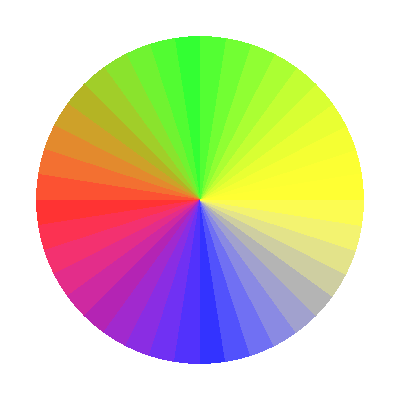

```mathematica
Remove["barColorFunc"]
barColorFunc=
Block[{hsbcolor=
ColorConvert[RGBColor[
Piecewise[{{Cos[#2],#2<π/2},{Sin[#2-π/2],And[#2>=π/2,#2<π*3/2]},{Sin[#2-π*3/2],#2≥π*3/2}}],
Piecewise[{{1,#2<π/2},{Sin[#2],And[#2≥π/2,#2<π]},{0,And[#2≥π,#2<π*3/2]},{Sin[#2-π*3/2],#2≥π*3/2}}],
Piecewise[{{0,#2<π},{Sin[#2-π],#2≥π}}]
]
,"HSB"]
}
,Hue[hsbcolor[[1]],hsbcolor[[2]]*0.8,hsbcolor[[3]]]]&;
Graphics[Map[{barColorFunc[0,#],Disk[{0,0},1,{#,#+2π/39}]}&,Range[0,2π,2π/40]]]
```

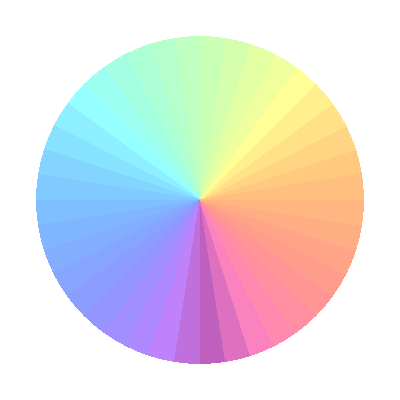

```mathematica
Remove["barColorFunc"]
barColorFunc=
Block[{hsbcolor=
ColorConvert[RGBColor[
Cos[#2/2]^2,
Sin[#2]/2+0.5,
1.0-Cos[#2/2]^2
]
,"HSB"]
}
,Hue[hsbcolor[[1]],hsbcolor[[2]]*0.5,hsbcolor[[3]]*1.5]]&;
Graphics[Map[{barColorFunc[0,#],Disk[{0,0},1,{#,#+2π/39}]}&,Range[0,2π,2π/40]]]
```

```mathematica
max = 0.01;
matrixplotid=matrixDraw3D[χIdeal,whatBarShape->"square",barDirectives->{Opacity[0],EdgeForm[{Black}]},arrowDirectives->{Opacity[0.8],Black,Thickness[0.005],Arrowheads[0]},ignoreCell->(#[[1]]>-#[[2]]&),barDiameter->0.4,hideBarSmallerThan->max,hideArrowSmallerThan->max,hideBarSmallerThan->max,arrowLength->(0.3&),frameFaceFunction->(GrayLevel[1-0.2KroneckerDelta[#1,-#2]]&)];
matrixplotphys=matrixDraw3D[χExp1Phys,whatBarShape->"square",barDirectives->{Opacity[1]},arrowDirectives->{Opacity[0.8],Black,Thickness[0.001],Arrowheads[0]},ignoreCell->(#[[1]]>-#[[2]]&),hideArrowSmallerThan->max,barDiameter->0.4,hideBarSmallerThan->max,arrowLength->(0.3&),frameFaceFunction->(GrayLevel[1-0.2KroneckerDelta[#1,-#2]]&),barColorFunction->barColorFunc];
```

```mathematica
chiMatrixPlot=Show[{matrixplotid,matrixplotphys},ViewPoint->10000{1.1,-1.1,1.5},BoxRatios->{1,1,0.5},Boxed->False,PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
matrixploterrorid=matrixDraw3D[χTildeIdeal,whatBarShape->"square",barDirectives->{Opacity[0],EdgeForm[{Black}]},arrowDirectives->{Opacity[0.8],Black,Thickness[0.002],Arrowheads[0]},ignoreCell->(#[[1]]<-#[[2]]&),barDiameter->0.4,hideBarSmallerThan->max,hideArrowSmallerThan->max,hideBarSmallerThan->max,arrowLength->(0.3&),frameFaceFunction->(GrayLevel[1-0.2KroneckerDelta[#1,-#2]]&)];
matrixploterror=matrixDraw3D[χTildeExp4Phys,whatBarShape->"square",barDirectives->{Opacity[1]},hideBarSmallerThan->max,hideArrowSmallerThan->max,arrowDirectives->{Opacity[0.8],Black,Thickness[0.001],Arrowheads[0]},ignoreCell->(#[[1]]<-#[[2]]&),barDiameter->0.4,arrowLength->(0.3&),frameFaceFunction->(GrayLevel[1-0.2KroneckerDelta[#1,-#2]]&),barColorFunction->barColorFunc];
errorMatrixPlot=Show[{matrixploterror,matrixploterrorid},ViewPoint->10000{1.1,-1.1,1.5},BoxRatios->{1,1,0.5},Boxed->False,PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"chi_matrix_plot.png",chiMatrixPlot,ImageResolution->300]
Export[NotebookDirectory[]<>"error_matrix_plot.png",errorMatrixPlot,ImageResolution->300]
```

D:\cygwin\home\adewes\thesis\data\ct5\2011_04_21 - grover and tomo\good_data\chi_matrix_plot.png

D:\cygwin\home\adewes\thesis\data\ct5\2011_04_21 - grover and tomo\good_data\error_matrix_plot.png